# BSE Hubbard

## Fonctions

```mathematica
Remove["Global`*"]
$PreRead=(#/.
s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`150."&);
```

```mathematica
Subscript[δ, a_,b_]:=KroneckerDelta[a,b]
```

```mathematica
SortEigensystem[eigsys_]:=Transpose[Sort[Transpose[eigsys]]]
```

```mathematica
SortEigensystemGreater[eigsys_]:=Transpose[Sort[Transpose[eigsys],Greater]]
```

```mathematica
TakeMOs[c_,n_]:=Transpose[Take[Transpose[c],n]]
```

```mathematica
DIIS[ℰ_,Δℰ_]:=Module[{nDIIS,B,X,w,ϵ},
nDIIS=Min[4,Length[Δℰ]];
B=Table[
Which[
i≤nDIIS∧j≤nDIIS,Flatten[Δℰ⟦i⟧].Flatten[Δℰ⟦j⟧],
i≤nDIIS∧j==nDIIS+1,-1,
i==nDIIS+1∧j≤nDIIS,-1,
i==nDIIS+1∨j==nDIIS+1,0
]
,{i,1,nDIIS+1},{j,1,nDIIS+1}];
X=Table[If[k≤nDIIS,0,-1],{k,1,nDIIS+1}];
w=LinearSolve[B,X];
ϵ=∑_(k=1)^nDIIS w⟦k⟧ℰ⟦k⟧;
Return[ϵ];
];
```

```mathematica
ℰ23as[t_,U_,Δv_]:=2/3 (U+ √(12 t^2+U^2+3 Δv^2) Cos[1/3 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/((12 t^2+U^2+3 Δv^2)^(3/2))]])
ℰ22as[t_,U_,Δv_]:=2/3 (U- √(12 t^2+U^2+3 Δv^2) Cos[1/3 (π+ArcCos[-(U (18 t^2+U^2-9 Δv^2))/((12 t^2+U^2+3 Δv^2)^(3/2))])])
ℰ21as=0;
ℰ20as[t_,U_,Δv_]:=2/3 (U- √(12 t^2+U^2+3 Δv^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/((12 t^2+U^2+3 Δv^2)^(3/2))])])
excas1[t_,U_,Δv_]:= - ℰ20as[t,U,Δv]
excas2[t_,U_,Δv_]:= ℰ22as[t,U,Δv]- ℰ20as[t,U,Δv]
excas3[t_,U_,Δv_]:= ℰ23as[t,U,Δv]- ℰ20as[t,U,Δv]
ωEAexcas[t_,U_,Δv_]:=-1/6 (2 U-3 t √(4+Δv^2/t^2)+4 t √((12 t^2+U^2+3 Δv^2)/t^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/(t^3 ((12 t^2+U^2+3 Δv^2)/t^2)^(3/2))])])
ωEIexcas[t_,U_,Δv_]:=-1/6 (4 U+3 t √(4+Δv^2/t^2)-4 t √((12 t^2+U^2+3 Δv^2)/t^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/(t^3 ((12 t^2+U^2+3 Δv^2)/t^2)^(3/2))])])
Egap[t_,U_,Δv_]:= ωEIexcas[t,U,Δv]-ωEAexcas[t,U,Δv]
Eb1exc[t_,U_,Δv_]:= Egap[t,U,Δv]-excas1[t,U,Δv]
Eb2exc[t_,U_,Δv_]:= Egap[t,U,Δv]-excas2[t,U,Δv]

N20as[t_,U_,Δv_]:= Sqrt[2+((2t)/(U-Δv-ℰ20as[t,U,Δv]))^2+((2t)/(U+Δv-ℰ20as[t,U,Δv]))^2]
N22as[t_,U_,Δv_]:= Sqrt[2+((2t)/(U-Δv-ℰ22as[t,U,Δv]))^2+((2t)/(U+Δv-ℰ22as[t,U,Δv]))^2]
N23as[t_,U_,Δv_]:= Sqrt[2+((2t)/(U-Δv-ℰ23as[t,U,Δv]))^2+((2t)/(U+Δv-ℰ23as[t,U,Δv]))^2]
f0n[t_,U_,Δv_]:= (8 t^2)/(N20as[t,U,Δv]N22as[t,U,Δv])(1/((U+Δv-ℰ20as[t,U,Δv])(U+Δv-ℰ22as[t,U,Δv]))-1/((U-Δv-ℰ20as[t,U,Δv])(U-Δv-ℰ22as[t,U,Δv])))
```

```mathematica
Densite[t_,U_,Δv_]:=Module[{E20as,E22as,E23as,𝒩20as,𝒩22as,𝒩10as,𝒩11as,n10,n20,n1ex2,n2ex2,n1tr2,n2tr2,c32,c42},
E20as[t,U,Δv]:=2/3 (U- √(12 t^2+U^2+3 Δv^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/((12 t^2+U^2+3 Δv^2)^(3/2))])]);E22as[t,U,Δv]:=2/3 (U- √(12 t^2+U^2+3 Δv^2) Cos[1/3 (π+ArcCos[-(U (18 t^2+U^2-9 Δv^2))/((12 t^2+U^2+3 Δv^2)^(3/2))])]);
E23as[U,Δv]:=2/3*(U-√(12 t^2+U^2+3 Δv^2)*Cos[1/3*ArcCos[(-(U^2+18 t^2-9 Δv^2)*U)/((U^2+12 t^2+3 Δv^2)^(3/2))]+π]);
𝒩10as[t,Δv]:=√(1+ (Δv/(2t)+(√(4 t^2+Δv^2))/(2t))^2);
𝒩11as[t,Δv]:=√(1+ (Δv/(2t)-(√(4 t^2+Δv^2))/(2t))^2);
𝒩20as[t,U,Δv]:=√(2+((2t)/(U+Δv-E20as[t,U,Δv]))^2+((2t)/(U-Δv-E20as[t,U,Δv]))^2);
𝒩22as[t,U,Δv]:=√(2+((2t)/(U+Δv-E22as[t,U,Δv]))^2+((2t)/(U-Δv-E22as[t,U,Δv]))^2);

n10[t,U,Δv]:=(1/𝒩20as[t,U,Δv])^2(2+8/(U+Δv-E20as[t,U,Δv])^2);
n20[t,U,Δv]:=(1/𝒩20as[t,U,Δv])^2(2+8/(U-Δv-E20as[t,U,Δv])^2);
n1ex2[t,U,Δv]:=(1/𝒩22as[t,U,Δv])^2(2+8/(U+Δv-E22as[t,U,Δv])^2);
n2ex2[t,U,Δv]:=(1/𝒩22as[t,U,Δv])^2(2+8/(U-Δv-E22as[t,U,Δv])^2);
n1tr2[t,U,Δv]:=(1/(𝒩20as[t,U,Δv]𝒩22as[t,U,Δv]))(2+8/((U+Δv-E20as[t,U,Δv])(U+Δv-E22as[t,U,Δv])));
n2tr2[t,U,Δv]:=(1/(𝒩20as[t,U,Δv]𝒩22as[t,U,Δv]))(2+8/((U-Δv-E20as[t,U,Δv])(U-Δv-E22as[t,U,Δv])));
c32[t,U,Δv]:=1/𝒩22as[t,U,Δv](2t)/(U+Δv-E22as[t,U,Δv]);
c42[t,U,Δv]:=1/𝒩22as[t,U,Δv](2t)/(U+Δv-E22as[t,U,Δv]);
Return[{n10[t,U,Δv],n20[t,U,Δv],n1ex2[t,U,Δv],n2ex2[t,U,Δv],n1tr2[t,U,Δv],n2tr2[t,U,Δv],c32[t,U,Δv],c42[t,U,Δv]}];
];
```

## Hartree-Fock

```mathematica
HubbardHF[t_,U_,Δv_]:=
Module[{nElec,nSite,maxSCF,thresh,F,T,V,H,ERI,J,K,c,O,ϵ,P,ϵ0,c0,nSCF,Conv,EHF,ET,EV,EJ,EK,Gap,TabRes,FDIIS,eDIIS,Δn,ℰ20as,EC},

nElec=2; nSite=2; maxSCF=1024; thresh=10^-5;

ℰ20as[t,U,Δv]:=2/3 (U- √(12 t^2+U^2+3 Δv^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/((12 t^2+U^2+3 Δv^2)^(3/2))])]);
T=({{0, -t}, {-t, 0}});              V=({{Δv/2, 0}, {0, -Δv/2}});
ERI=Table[U Subscript[δ, μ,λ] Subscript[δ, ν,σ] Subscript[δ, μ,ν],{μ,nSite},{ν,nSite},{λ,nSite},{σ,nSite}];

H=T+V;           J=Flatten[ERI,{{1},{3},{2,4}}];         K=Flatten[ERI,{{1},{4},{2,3}}];    
{ϵ,c}=Chop[SortEigensystem[Eigensystem[H]]];

c=Transpose[c];       O=TakeMOs[c,nElec/2];
c=Table[Normalize[c[[i]]],{i,Length[c]}];
{ϵ0,c0}={ϵ,c};

Conv=1;    nSCF=0;(*Conv>thresh∧nSCF<maxSCF*) FDIIS={}; eDIIS={};
(*While[Conv>thresh∧nSCF<maxSCF,
nSCF++;
P=2O.O^ᵀ;    F=H+(J-1/2 K).Flatten[P];
FDIIS=Prepend[FDIIS,F];	eDIIS=Prepend[eDIIS,F.P-P.F];
F=DIIS[FDIIS,eDIIS];
{ϵ,c}=Chop[SortEigensystem[Eigensystem[F]]];
c=cᵀ ;      O=TakeMOs[c,nElec/2];
Conv=Max[Abs[F.P-P.F]];
(*If[nSCF==1,Print[MatrixForm[(J-1/2 K).Flatten[P]]]];*)
];
If[nSCF==maxSCF,Print["Convergence issue for {t,U,Δv} = ",{t,U,Δv},Conv]];
Gap=ϵ⟦nElec/2+1⟧-ϵ⟦nElec/2⟧;
ET=Tr[P.T];      EV=Tr[P.V];
EJ=Tr[P.J.Flatten[P]]/2;          EK=-Tr[P.K.Flatten[P]]/4 ;
EHF=ET+EV+EJ+EK;
EC=ℰ20as[t,U,Δv]-EHF;

TabRes=TableForm[{{nElec,nSite,NumberForm[EHF,{9,6}],NumberForm[ET,{9,6}],NumberForm[EV,{9,6}],NumberForm[EJ,{9,6}],NumberForm[EK,{9,6}],nSCF,NumberForm[Conv,{6,3}],NumberForm[Gap,{6,3}]}},
TableHeadings->{None,{"N_elec","N_site","E_HF","T_HF","V_HF","J_HF","K_HF","N_SCF","Conv","HL Gap"}},TableAlignments->Center];*);
Return[{c,ϵ,Gap,c0,ϵ0}];

];
```

## Quasiparticules

### Quasiparticules GW

#### Spin orbitales

```mathematica
HubbardGWSpinOrb[t_,U_,Δv_]:=Module[{η,eps,ϵQPlin,ϵQP,c,c1,c2,c1p,c2p,intb,A,B,R,χ,w,no,nv,nBas,ia,jb,ij,ab,i,b,a,j,p,Ω,ℰ,𝒱,V,Xs,Ys,n,Σ,dΣ,dΣω,Z,z,zω,tmp,e,eqp,eo,eqpo,eqpv,ev,Wijba,Wibja,S1,Sinv,A1,B1,H1,ω1,V1,A3,B3,H3,ω3,V3,Eg,Eb1,Eb3,l,ERI,O,XpY,XmY,X,Y,eqposcf,eqpvscf,E1,E3,ℰ20as,EC,M,Zsites},
η=0;

{c,eps}=HubbardHF[t,U,Δv]⟦1;;2⟧;
c1=c⟦1,1⟧;c2=c⟦2,1⟧;c1p=c⟦1,2⟧;c2p=c⟦2,2⟧;
eqp={};

no=1;
nv=1;
nBas=no+nv;
eo=eps[[1;;no]];
ev=eps[[no+1;;nBas]];

ERI=Table[U Subscript[δ, μ,λ] Subscript[δ, ν,σ] Subscript[δ, μ,ν],{μ,nBas},{ν,nBas},{λ,nBas},{σ,nBas}];
intb=Table[0,{p,nBas},{q,nBas},{r,nBas},{s,nBas}];
intb= cᵀ.Transpose[cᵀ.ERI.c,{2,1,4,3}].c;
intb=Table[Subscript[δ, Mod[p,2],Mod[r,2]] Subscript[δ, Mod[s,2],Mod[q,2]] intb⟦⌊(p+1)/2⌋,⌊(q+1)/2⌋,⌊(r+1)/2⌋,⌊(s+1)/2⌋⟧,{p,2nBas},{q,2nBas},{r,2nBas},{s,2nBas}];
eps=Table[eps⟦⌊(p+1)/2⌋⟧,{p,2nBas}];
no=2;
nv=2;
nBas=no+nv;

eo=eps[[1;;no]];
ev=eps[[no+1;;nBas]];


A=Table[Subscript[δ, i,j]*Subscript[δ, a,b]*(ev[[a]]-eo[[i]])+intb[[i]][[b+no]][[a+no]][[j]],{i,no},{a,nv},{j,no},{b,nv}];
A=Flatten[A,{{1,2},{3,4}}];
B=Table[intb[[i]][[j]][[a+no]][[b+no]],{i,no},{a,nv},{j,no},{b,nv}];
B=Flatten[B,{{1,2},{3,4}}];

R=ArrayFlatten[({{A, B}, {-B, -A}})];
{Ω,V}=SortEigensystem[Eigensystem[R]];
ℰ=Ω;
𝒱=Vᵀ;
EC=0.5Total[Ω]-0.5Tr[A];
V=V⟦no*nv+1;;2no*nv⟧;
Ω=Ω⟦no*nv+1;;2no*nv⟧;

X=V⟦1;;no*nv,1;;no*nv⟧ᵀ;
Y=V⟦1;;no*nv,no*nv+1;;2no*nv⟧ᵀ;

Xs=X;
Ys=Y;

n=Xᵀ.X-Yᵀ.Y;
X=X.MatrixPower[n,-1/2];
Y=Y.MatrixPower[n,-1/2];

w=ConstantArray[0,{nBas,nBas,no*nv}];
Do[
Do[
Do[
ia=1;
Do[
Do[
w⟦p,q,m⟧=w⟦p,q,m⟧+intb⟦p,i,q,a⟧*(X⟦ia,m⟧+Y⟦ia,m⟧);
ia++,{i,no}],{a,no+1,nBas}],{q,nBas}]
,{p,nBas}],{m,no*nv}];


Wpqrs=Table[intb⟦p,r,q,s⟧+∑_(m=1)^(no nv) w[[p,q,m]]w[[r,s,m]](1/(0-Ω[[m]]+ⅈ η)-1/(0+Ω[[m]]-ⅈ η)),{p,nBas},{q,nBas},{r,nBas},{s,nBas}];
Wijba=Table[intb[[i]][[b+no]][[j]][[a+no]]+∑_(m=1)^(no nv) w[[i,j,m]]w[[b+no,a+no,m]](1/(0-Ω[[m]]+ⅈ η)-1/(0+Ω[[m]]-ⅈ η)),{i,no},{j,no},{b,nv},{a,nv}];
Wibja=Table[intb[[i]][[j]][[b+no]][[a+no]]+∑_(m=1)^(no nv) w[[i,b+no,m]]w[[j,a+no,m]](1/(0-Ω[[m]]+ⅈ η)-1/(0+Ω[[m]]-ⅈ η)),{i,no},{b,nv},{j,no},{a,nv}];


Σ=Table[∑_(i=1)^no ∑_(m=1)^(no nv) w[[p,i,m]]^2/(ω-eo[[i]]+Ω[[m]]-ⅈ η)+∑_(a=1)^nv ∑_(m=1)^(no nv) w[[p,a+no,m]]^2/(ω-ev[[a]]-Ω[[m]]+ⅈ η),{p,nBas}];
(*∑_(i=1)^no (intb[[p]][[i]][[p]][[i]]-intb[[p]][[i]][[i]][[p]])+*)
dΣ=Table[-∑_(i=1)^no ∑_(m=1)^(no nv) w[[p,i,m]]^2/(ω-eo[[i]]+Ω[[m]]-ⅈ η)^2-∑_(a=1)^nv ∑_(m=1)^(no nv) w[[p,a+no,m]]^2/(ω-ev[[a]]-Ω[[m]]+ⅈ η)^2,{p,nBas}];
z=Table[(1-dΣ⟦p⟧)^-1/.ω->eps⟦p⟧,{p,nBas}];

ϵQPlin=Table[eps[[p]]+z[[p]]*Σ[[p]]/.ω->eps⟦p⟧,{p,nBas}] ;
ϵQP=Table[ω/.Solve[ω==eps⟦p⟧+Σ⟦p⟧,ω],{p,nBas}];

eqpo=ϵQPlin[[1;;no]];
eqpv=ϵQPlin[[no+1;;no+nv]];

eqposcf=ϵQPlin[[1;;no]];
eqpvscf=ϵQPlin[[no+1;;no+nv]];

Eg=Min[eqpv]-Max[eqpo];

l1={Ω,w,ϵQPlin,eqpo,eqpv,Wijba,Ω[[1]],Eg};
l2={Ω,w,eqp};
(*Print["Σ = ",Σ];
Print["Poids z linéarisé = ",z];
Print["Poids zω = ",zω];
Print["energies orbitales HF linéarisées",ϵQPlin];
Print["energies orbitales HF zω",ϵQP];*)
Return[l1];
];
```

#### Orbitales spatiales

```mathematica
HubbardGW[t_,U_,Δv_]:=Module[{η,eps,ϵQPlin,ϵQP,c,c1,c2,c1p,c2p,intb,A,B,R,w,no,nv,nBas,ia,jb,ij,ab,i,b,a,j,p,Ω,V,Xs,Ys,n,Σ,dΣ,dΣω,z,eqp,eo,eqpo,eqpv,ev,Wijba,Wibja,A1,B1,H1,ω1,V1,A3,B3,H3,ω3,V3,Eg,Eb1,Eb3,l,ERI,O,XpY,XmY,X,Y},
η=0;

{c,eps}=HubbardHF[t,U,Δv]⟦1;;2⟧;
c1=c⟦1,1⟧;c2=c⟦2,1⟧;c1p=c⟦1,2⟧;c2p=c⟦2,2⟧;
eqp={};


no=1;
nv=1;
nBas=no+nv;
eo=eps[[1;;no]];
ev=eps[[no+1;;nBas]];


intb=Table[0,{p,nBas},{q,nBas},{r,nBas},{s,nBas}];
ERI=Table[U Subscript[δ, μ,λ] Subscript[δ, ν,σ] Subscript[δ, μ,ν],{μ,nBas},{ν,nBas},{λ,nBas},{σ,nBas}];
intb= cᵀ.Transpose[cᵀ.ERI.c,{2,1,4,3}].c;

A=Table[Subscript[δ, i,j]*Subscript[δ, a,b]*(ev[[a]]-eo[[i]])+2intb[[i,b+no,a+no,j]],{i,no},{a,nv},{j,no},{b,nv}];
A=Flatten[A,{{1,2},{3,4}}];
B=Table[2intb[[i,j,a+no,b+no]],{i,no},{a,nv},{j,no},{b,nv}];
B=Flatten[B,{{1,2},{3,4}}];

R=ArrayFlatten[({{A, B}, {-B, -A}})];
{Ω,V}=SortEigensystem[Eigensystem[R]];
Ω=Ω[[no*nv+1;;2*no*nv]](*Select[Ω,Positive]*);
V    =Vᵀ;

Xs  =V[[1;;no*nv,no*nv+1;;2*no*nv]];
Ys  =V[[no*nv+1;;2*no*nv,no*nv+1;;2*no*nv]];
n=Xsᵀ.Xs-Ysᵀ.Ys;
Xs=1/(√n)Xs;
Ys=1/(√n)Ys;


O=MatrixPower[A-B,1/2];
{Ω,Z}=SortEigensystem[Eigensystem[O.(A+B).O]];	Ω=Ω^(1/2);	Z=Zᵀ;
XpY=DiagonalMatrix[Ω^(-1/2)].MatrixPower[A-B,1/2].Z;
XmY=DiagonalMatrix[Ω^(1/2)].MatrixPower[A-B,-1/2].Z;
X=(XpY+XmY)/2;
Y=(XpY-XmY)/2;
n=Xᵀ.X-Yᵀ.Y;
X=X/(√n);
Y=Y/(√n);

w=ConstantArray[0,{nBas,nBas,no*nv}];

w=Table[
jb=0;
Sum[(jb++;intb⟦p,j,q,b⟧(X+Y)⟦jb,ia⟧),{j,no},{b,no+1,nBas}],
{p,nBas},{q,nBas},{ia,no nv}];


Wpqrs=Table[intb⟦p,q,r,s⟧+2∑_(m=1)^(no nv) w⟦p,r,m⟧w⟦q,s,m⟧(1/(0-Ω[[m]]+ⅈ η)-1/(0+Ω[[m]]-ⅈ η)),{p,nBas},{q,nBas},{r,nBas},{s,nBas}];
Wijba=Table[intb⟦i,b,j,a⟧+2∑_(m=1)^(no nv) w⟦i,j,m⟧w⟦b,a,m⟧(1/(0-Ω[[m]]+ⅈ η)-1/(0+Ω[[m]]-ⅈ η)),{i,no},{j,no},{b,no+1,nBas},{a,no+1,nBas}];
Wibja=Table[intb⟦i,j,b,a⟧+2∑_(m=1)^(no nv) w⟦i,b,m⟧w⟦j,a,m⟧(1/(0-Ω[[m]]+ⅈ η)-1/(0+Ω[[m]]-ⅈ η)),{i,no},{b,no+1,nBas},{j,no},{a,no+1,nBas}];
Σ=Table[2∑_(i=1)^no ∑_(m=1)^(no nv) w⟦p,i,m⟧^2/(ω-eo⟦i⟧+Ω⟦m⟧-ⅈ η)+2∑_(a=1)^nv ∑_(m=1)^(no nv) w⟦p,a+no,m⟧^2/(ω-ev⟦a⟧-Ω⟦m⟧+ⅈ η),{p,nBas}];
(* ∑_(i=1)^no (2intb[[p,i,p,i]]-intb[[p,i,i,p]])+ *)
dΣ=Table[-2∑_(i=1)^no ∑_(m=1)^(no nv) w[[p,i,m]]^2/(ω-eo[[i]]+Ω[[m]]-ⅈ η)^2-2∑_(a=1)^nv ∑_(m=1)^(no nv) w[[p,a+no,m]]^2/(ω-ev[[a]]-Ω[[m]]+ⅈ η)^2,{p,nBas}];
z=Table[(1-dΣ⟦p⟧)^-1/.ω->eps⟦p⟧,{p,nBas}];

ϵQPlin=Table[eps[[p]]+z[[p]]*Σ[[p]]/.ω->eps⟦p⟧,{p,nBas}] ;
(*ϵQP=Table[ω/.Solve[ω==eps⟦p⟧+Σ⟦p⟧,ω],{p,nBas}];*)
(*If[Δv == 0,zω=Table[(1-dΣ⟦p⟧)^-1/.ω->ϵQP⟦p,q⟧,{p,nBas},{q,2}],zω=Table[(1-dΣ⟦p⟧)^-1/.ω->ϵQP⟦p,q⟧,{p,nBas},{q,3}]];*)


eqpo=ϵQPlin[[1;;no]];
eqpv=ϵQPlin[[no+1;;no+nv]];

Eg=Min[eqpv]-Max[eqpo];

l1={Ω,w,ϵQPlin,eqpo,eqpv,Wijba,Ω[[1]],Eg};

(*Print["Σ = ",Σ];
Print["Poids z linéarisé = ",z];
Print["Poids zω = ",zω];
Print["energies orbitales HF linéarisées",ϵQPlin];
Print["energies orbitales HF zω",ϵQP];*)
Return[l1];
];
```

### Quasiparticules GT^pp

#### Orbitales spatiales

```mathematica
HubbardGT[t_,U_,Δv_]:=Module[{no,nv,nBas,noo,nvv,ERI,intb,Aαβ,Bαβ,Cαβ,Rαβ,Ωαβ,Vαβ,Ω1,Ω2,X1,Y1,X2,Y2,𝒩1,𝒩2,N1,N2,χ1αβ,χ2αβ,ab,cd,kl,a,b,c,c1,c2,c1p,c2p,d,i,j,k,l,p,χ1,χ2,χ3,χ4,Σ,dΣ,Z,Zsites,tmp,T,Tijba,Tibja,eqp,eo,eqpo,eqpv,ev,𝒜,ℬ,ℋ,ω,Eg,Eb,eps,η=0,Ivv,Ioo,O1,O2,Z1,Z2,M,S1,S2},

no=1;
nv=1;
noo=no^2;
nvv=nv^2;
eqp={};
nBas=no+nv;

{c,eps}=HubbardHF[t,U,Δv]⟦1;;2⟧;
c1=c⟦1,1⟧;c2=c⟦2,1⟧;c1p=c⟦1,2⟧;c2p=c⟦2,2⟧;
eo=eps[[1;;no]];
ev=eps[[no+1;;no+nv]];

ERI=Table[U Subscript[δ, μ,λ] Subscript[δ, ν,σ] Subscript[δ, μ,ν],{μ,nBas},{ν,nBas},{λ,nBas},{σ,nBas}];
intb= cᵀ.Transpose[cᵀ.ERI.c,{2,1,4,3}].c;


(* pp-RPA problem *)

Aαβ=Table[Subscript[δ, a,c] Subscript[δ, b,d](ev[[a]]+ev[[b]])+intb[[a+no,b+no,c+no,d+no]],{a,nv},{b,nv},{c,nv},{d,nv}];
Aαβ=Flatten[Aαβ,{{1,2},{3,4}}];
Bαβ=Table[intb[[a,b,i,j]],{a,no+1,nBas},{b,no+1,nBas},{i,1,no},{j,1,no}];
Bαβ=Flatten[Bαβ,{{1,2},{3,4}}];
Cαβ=Table[-Subscript[δ, i,k] Subscript[δ, j,l](eo[[i]]+eo[[j]])+intb[[i,j,k,l]],{i,1,no},{j,1,no},{k,1,no},{l,1,no}];
Cαβ=Flatten[Cαβ,{{1,2},{3,4}}];
Rαβ=ArrayFlatten[({{Aαβ, Bαβ}, {-Bαβᵀ, -Cαβ}})];
{Ωαβ,Vαβ}=SortEigensystemGreater[Eigensystem[Rαβ]];Vαβ=Vαβᵀ;
Ω1=Ωαβ⟦1;;nvv⟧;
Ω2=Ωαβ⟦nvv+1;;nvv+noo⟧;

Ivv=IdentityMatrix[nvv];
Ioo=IdentityMatrix[noo];
M= ArrayFlatten[({{Ivv, 0}, {0, -Ioo}})];

χ1αβ =ConstantArray[0,{nBas,nBas,nvv}];
χ2αβ =ConstantArray[0,{nBas,nBas,noo}];
Z1=Vαβ⟦1;;nvv+noo,1;;nvv⟧;
Z2=Vαβ⟦1;;nvv+noo,nvv+1;;nvv+noo⟧;

S1=+Z1ᵀ.M.Z1;
S2=-Z2ᵀ.M.Z2;

O1=MatrixPower[S1,-1/2];
O2=MatrixPower[S2,-1/2];
Z1 = Z1.O1;
Z2 = Z2.O2;

Y1=Z1⟦1;;nvv,1;;nvv⟧;
X1=Z1⟦nvv+1;;nvv+noo,1;;nvv⟧;
Y2=-Z2⟦1;;nvv,1;;noo⟧;
X2=-Z2⟦nvv+1;;nvv+noo,1;;noo⟧;

Do[
Do[
Do[
cd=1;
Do[
Do[
χ1αβ[[p,q,ab]]=χ1αβ[[p,q,ab]]+(intb[[p,q,c,d]])X1[[cd,ab]];
cd++
,{c,no+1,nBas}]
,{d,no+1,nBas}];

kl=1;
Do[
Do[
χ1αβ[[p,q,ab]]=χ1αβ[[p,q,ab]]+(intb[[p,q,k,l]])Y1[[kl,ab]];
kl++
,{k,no}]
,{l,no}]
,{q,nBas}]
,{p,nBas}]
,{ab,nvv}];


Do[
Do[
Do[
cd=1;
Do[
Do[
χ2αβ[[p,q,ij]]=χ2αβ[[p,q,ij]]+(intb[[p,q,c,d]])X2[[cd,ij]];
cd++,{c,no+1,nBas}],{d,no+1,nBas}];

kl=1;
Do[
Do[
χ2αβ[[p,q,ij]]=χ2αβ[[p,q,ij]]+(intb[[p,q,k,l]])Y2[[kl,ij]];
kl++,{k,no}],{l,no}],
{q,nBas}]
,{p,nBas}],{ij,noo}];

Σ=Table[∑_(i=1)^no ∑_(ab=1)^nvv (χ1αβ[[p,i,ab]]χ1αβ[[q,i,ab]])/(eps[[p]]+eo[[i]]-Ω1[[ab]]+ⅈ η)+∑_(a=1)^nv ∑_(ij=1)^noo (χ2αβ[[p,a+no,ij]]χ2αβ[[q,a+no,ij]])/(eps[[p]]+ev[[a]]-Ω2[[ij]]-ⅈ η),{p,nBas},{q,nBas}];
(*Σ=Table[∑_(i=1)^no (2intb[[p]][[i]][[p]][[i]]-intb[[p]][[i]][[i]][[p]]);*)
dΣ=Table[-∑_(i=1)^no ∑_(ab=1)^nvv (χ1αβ[[p,i,ab]]χ1αβ[[q,i,ab]])/(eps[[p]]+eo[[i]]-Ω1[[ab]]+ⅈ η)^2-∑_(a=1)^nv ∑_(ij=1)^noo (χ2αβ[[p,a+no,ij]]χ2αβ[[q,a+no,ij]])/(eps[[p]]+ev[[a]]-Ω2[[ij]]-ⅈ η)^2,{p,nBas},{q,nBas}];
Z=Table[(1-dΣ⟦p,p⟧)^-1,{p,nBas}];
eqp=Table[eps[[p]]+Z[[p]]*Σ[[p,p]],{p,nBas}] ;
Ghfinv=Table[(ω-eps[[p]])Subscript[δ, p,q],{p,1,nBas},{q,1,nBas}];
Ghf = Inverse[Ghfinv];

eqpo=eqp[[1;;no]];
eqpv=eqp[[no+1;;no+nv]];
Eg=Min[eqpv]-Max[eqpo];

Return[{Ω1,Ω2,eqp,X1,Y1,X2,Y2,Eg}];
];
```

### Quasiparticules GT^ph

#### Spin orbitales

```mathematica
HubbardGTehSpinOrb[t_,U_,Δv_]:=Module[{η=0,eps,ϵQPlin,ϵQP, intb, no, nv, nBas,f0nhf,c,c1,c2,c1p,c2p,A,B,R,X,Y,n,Ro,μ,f,ia,jb,i,b,a,j,Ω,V,S,Xs,Ys,Σ,dΣ,dΣω,z,eqp,eo,ev,eqpo,eqpv,Teh,𝒜,ℬ,ℋ,V1,ω1,V3,Eg,Eb1,Eb3,l3,l1,ERI,χl,χr,𝒱,𝒶,𝒷,𝒷p,𝒸,ℋt,Vt,Xt,Yt,nt,λt,ℋs,Vs,ns,λs},

{c,eps}=HubbardHF[t,U,Δv]⟦1;;2⟧;
c1=c⟦1,1⟧;c2=c⟦2,1⟧;c1p=c⟦1,2⟧;c2p=c⟦2,2⟧;
f0nhf= 2 √2(c1^3 c1p-c2^3 c2p);
eqp={};
no=1;
nv=1;
nBas=no+nv;
eo=eps[[1;;no]];
ev=eps[[no+1;;nBas]];

ERI=Table[U Subscript[δ, μ,λ] Subscript[δ, ν,σ] Subscript[δ, μ,ν],{μ,nBas},{ν,nBas},{λ,nBas},{σ,nBas}];
intb=Table[0,{p,nBas},{q,nBas},{r,nBas},{s,nBas}];
intb= cᵀ.Transpose[cᵀ.ERI.c,{2,1,4,3}].c;
intb=Table[Subscript[δ, Mod[p,2],Mod[r,2]] Subscript[δ, Mod[s,2],Mod[q,2]] intb⟦⌊(p+1)/2⌋,⌊(q+1)/2⌋,⌊(r+1)/2⌋,⌊(s+1)/2⌋⟧,{p,2nBas},{q,2nBas},{r,2nBas},{s,2nBas}];
eps=Table[eps⟦⌊(p+1)/2⌋⟧,{p,2nBas}];
no=2;
nv=2;
nBas=no+nv;

eo=eps⟦1;;no⟧;
ev=eps⟦no+1;;nBas⟧;

A=Table[Subscript[δ, i,j]*Subscript[δ, a,b]*(ev⟦a⟧-eo⟦i⟧)-intb⟦a+no,j,b+no,i⟧,{i,no},{a,nv},{j,no},{b,nv}];
A=Flatten[A,{{1,2},{3,4}}];
B=Table[-intb⟦a+no,b+no,j,i⟧,{i,no},{a,nv},{j,no},{b,nv}];
B=Flatten[B,{{1,2},{3,4}}];
R=ArrayFlatten[({{A, B}, {-B, -A}})];

{Ω,V}=SortEigensystem[Eigensystem[R]];
𝒱=Vᵀ;
V=V⟦no*nv+1;;2no*nv⟧;
Ω=Ω⟦no*nv+1;;2no*nv⟧;

Xs=V⟦1;;no*nv,1;;no*nv⟧ᵀ;
Ys=V⟦1;;no*nv,no*nv+1;;2no*nv⟧ᵀ;

n=Xsᵀ.Xs-Ysᵀ.Ys;
Xs=Xs.MatrixPower[n,-1/2];
Ys=Ys.MatrixPower[n,-1/2];
χl=ConstantArray[0,{nBas,nBas,no*nv}];
χr=ConstantArray[0,{nBas,nBas,no*nv}];

Do[
Do[
Do[
jb=1;
Do[
Do[
χl⟦p,q,m⟧+=intb⟦p,j,b,q⟧Xs⟦jb,m⟧+intb⟦p,b,j,q⟧Ys⟦jb,m⟧;
jb++
,{j,no}]
,{b,no+1,nBas}]
,{q,nBas}]
,{p,nBas}]
,{m,no*nv}];


Do[
Do[
Do[
jb=1;
Do[
Do[
χr⟦p,q,m⟧+=intb⟦p,j,b,q⟧Xs⟦jb,m⟧+intb⟦p,b,j,q⟧Ys⟦jb,m⟧-intb⟦j,p,b,q⟧(Xs⟦jb,m⟧+Ys⟦jb,m⟧);
jb++
,{j,no}]
,{b,no+1,nBas}]
,{q,nBas}]
,{p,nBas}]
,{m,no*nv}];

Teh=Table[intb⟦p,q,r,s⟧-intb⟦p,q,s,r⟧-∑_(m=1)^(no nv) ((χl⟦p,s,m⟧χr⟦r,q,m⟧)/(0-Ω[[m]]+ⅈ η)-(χl⟦s,p,m⟧χr⟦q,r,m⟧)/(0+Ω[[m]]-ⅈ η)),{p,nBas},{q,nBas},{r,nBas},{s,nBas}];
Σ=Table[∑_(i=1)^no (intb[[p,i,p,i]]-intb[[p,i,i,p]])+∑_(i=1)^no ∑_(m=1)^(no nv) (χl⟦i,p,m⟧χr⟦i,p,m⟧)/(ω-eo⟦i⟧+Ω⟦m⟧-ⅈ η)+∑_(a=1)^nv ∑_(m=1)^(no nv) (χl⟦p,a+no,m⟧χr⟦p,a+no,m⟧)/(ω-ev⟦a⟧-Ω⟦m⟧+ⅈ η),{p,nBas}];
(*∑_(i=1)^no (intb[[p,i,p,i]]-intb[[p,i,i,p]])+*)
dΣ=Table[-∑_(i=1)^no ∑_(m=1)^(no nv) (χl⟦i,p,m⟧χr⟦i,p,m⟧)/(ω-eo[[i]]+Ω[[m]]-ⅈ η)^2-∑_(a=1)^nv ∑_(m=1)^(no nv) (χl⟦p,a+no,m⟧χr⟦p,a+no,m⟧)/(ω-ev[[a]]-Ω[[m]]+ⅈ η)^2,{p,nBas}];
z=Table[(1-dΣ⟦p⟧)^-1/.ω->eps⟦p⟧,{p,nBas}];

ϵQPlin=Table[eps[[p]]+z[[p]]*Σ[[p]]/.ω->eps⟦p⟧,{p,nBas}] ;
(*ϵQP=Table[ω/.Solve[ω==eps⟦p⟧+Σ⟦p⟧,ω],{p,nBas}];*);
eqpo=ϵQPlin[[1;;no]];
eqpv=ϵQPlin[[no+1;;nBas]];


Eg=Min[eqpv]-Max[eqpo];
𝒜=Table[Subscript[δ, i,j]*Subscript[δ, a,b]*(eqpv[[a]]-eqpo[[i]])+Teh⟦i,b+no,a+no,j⟧,{i,no},{a,nv},{j,no},{b,nv}];
𝒜=Flatten[𝒜,{{1,2},{3,4}}];
ℬ=Table[Teh⟦i,j,a+no,b+no⟧,{i,no},{a,nv},{j,no},{b,nv}];
ℬ=Flatten[ℬ,{{1,2},{3,4}}];
ℋ=ArrayFlatten[({{𝒜, ℬ}, {-ℬ, -𝒜}})];
{ω1,V1}=SortEigensystem[Eigensystem[ℋ]];

(*X=V1⟦1;;no*nv,1;;no*nv⟧ᵀ;
Y=V1⟦1;;no*nv,no*nv+1;;2no*nv⟧ᵀ;
n  =Xᵀ.X-Yᵀ.Y*);

𝒶  =ℋ⟦1,1⟧;
𝒷  =ℋ⟦1,4⟧;
𝒷p=ℋ⟦1,8⟧;
𝒸   =ℋ⟦1,5⟧;

ℋt=({{𝒶-𝒷, -𝒷p+𝒸}, {-(-𝒷p+𝒸), -(𝒶-𝒷)}});

ℋs=({{𝒶+𝒷, 𝒷p+𝒸}, {-(𝒷p+𝒸), -(𝒶+𝒷)}});

{λt,Vt}=SortEigensystem[Eigensystem[ℋt]];
{λs,Vs}=SortEigensystem[Eigensystem[ℋs]];
λt=Select[λt,Positive];
λs=Select[λs,Positive];
no=1;
nv=1;

Vs=Vs⟦no*nv+1;;2no*nv⟧;
X=Vs⟦1;;no*nv,1;;no*nv⟧ᵀ;
Y=Vs⟦1;;no*nv,no*nv+1;;2no*nv⟧ᵀ;

ns=Xᵀ.X-Yᵀ.Y;
X=X.MatrixPower[ns,-1/2];
Y=Y.MatrixPower[ns,-1/2];
μ= f0nhf(X+Y)[[1,1]];
f= 2/3 λs[[1]] μ^2;

Xt=Vt⟦1;;no*nv,1;;no*nv⟧ᵀ;
Yt=Vt⟦1;;no*nv,no*nv+1;;2no*nv⟧ᵀ;

nt=Xtᵀ.Xt-Ytᵀ.Yt;
Xt=Xt.MatrixPower[nt,-1/2];
Yt=Yt.MatrixPower[nt,-1/2]; 
eqp={eqpo[[1]],eqpv[[1]]};
Eb3=Eg-ω1[[5]];
Eb1=Eg-ω1[[8]];

l3={Eg,ω1[[5]],Eb3,f0nhf,nt⟦1,1⟧,eqp};
l1={Eg,ω1[[8]],Eb1,f,Ω};

Return[{l3,l1}];
];
```

#### BSET^ph G^0

```mathematica
BSETphG0[t_,U_,Δv_]:=Module[{no,nv,c10,c20,c11,c21,d,dt,Σ11,Σ12,Σ22,dΣ11,dΣ12,dΣ22,Σvv,Σcc,dΣvv,dΣcc,Zvv,Zcc,A,B,ϵv,ϵc,Δϵ,O1111,O1221,T1111,T1221,T1vcvc,T1vccv,𝒜,ℬ,ℋ,V,λ,ℋt,Vt,λt,Xt,Yt,nt,ℋs,Vs,λs,X,Y,n,f0nhf,f,μ,lt,ls},

no=1;
nv=1;
c10[t,Δv]:=1/(√(1+(Δv/(2t)+√((Δv/(2t))^2+1))^2));c20[t,Δv]:=(Δv/(2t)+√((Δv/(2t))^2+1))/(√(1+(Δv/(2t)+√((Δv/(2t))^2+1))^2)); 
c11[t,Δv]:=1/(√(1+(Δv/(2t)-√((Δv/(2t))^2+1))^2));c21[t,Δv]:=(Δv/(2t)-√((Δv/(2t))^2+1))/(√(1+(Δv/(2t)-√((Δv/(2t))^2+1))^2));
f0nhf= 2 √2(c10[t,Δv]^3 c11[t,Δv]-c20[t,Δv]^3 c21[t,Δv]);
d[t,Δv]:=√(4 t^2+Δv^2); dt[t,U,Δv]:=√(d[t,Δv]^2-(4U t^2)/d[t,Δv]);
A[t,Δv]:=1/2-Δv/(2d[t,Δv]);B[t,Δv]:=1/2+Δv/(2d[t,Δv]);
Σ11[ω_,t,U,Δv]:=A[t,Δv]U+(U^2 t^2)/(d[t,Δv]dt[t,U,Δv])(B[t,Δv]/(ω-(d[t,Δv]/2+dt[t,U,Δv]))+A[t,Δv]/(ω+(d[t,Δv]/2+dt[t,U,Δv])));
Σ22[ω_,t,U,Δv]:=B[t,Δv]U+(U^2 t^2)/(d[t,Δv]dt[t,U,Δv])(A[t,Δv]/(ω-(d[t,Δv]/2+dt[t,U,Δv]))+B[t,Δv]/(ω+(d[t,Δv]/2+dt[t,U,Δv])));
Σ12[ω_,t,U,Δv]:=(U^2 t^3)/(d[t,Δv]^2 dt[t,U,Δv])(1/(ω-(d[t,Δv]/2+dt[t,U,Δv]))-1/(ω+(d[t,Δv]/2+dt[t,U,Δv])));
dΣ11[ω_,t,U,Δv]:=-(U^2 t^2)/(d[t,Δv]dt[t,U,Δv])(B[t,Δv]/(ω-(d[t,Δv]/2+dt[t,U,Δv]))^2+A[t,Δv]/(ω+(d[t,Δv]/2+dt[t,U,Δv]))^2);
dΣ22[ω_,t,U,Δv]:=-(U^2 t^2)/(d[t,Δv]dt[t,U,Δv])(A[t,Δv]/(ω-(d[t,Δv]/2+dt[t,U,Δv]))^2+B[t,Δv]/(ω+(d[t,Δv]/2+dt[t,U,Δv]))^2);
dΣ12[ω_,t,U,Δv]:=-(U^2 t^3)/(d[t,Δv]^2 dt[t,U,Δv])(1/(ω-(d[t,Δv]/2+dt[t,U,Δv]))^2-1/(ω+(d[t,Δv]/2+dt[t,U,Δv]))^2);

Σvv[ω_,t,U,Δv]:=c10[t,Δv]^2 Σ11[ω,t,U,Δv]+2c10[t,Δv]c20[t,Δv]Σ12[ω,t,U,Δv]+c20[t,Δv]^2 Σ22[ω,t,U,Δv];
Σcc[ω_,t,U,Δv]:=c11[t,Δv]^2 Σ11[ω,t,U,Δv]+2c11[t,Δv]c21[t,Δv]Σ12[ω,t,U,Δv]+c21[t,Δv]^2 Σ22[ω,t,U,Δv];
dΣvv[ω_,t,U,Δv]:=c10[t,Δv]^2 dΣ11[ω,t,U,Δv]+2c10[t,Δv]c20[t,Δv]dΣ12[ω,t,U,Δv]+c20[t,Δv]^2 dΣ22[ω,t,U,Δv];
dΣcc[ω_,t,U,Δv]:=c11[t,Δv]^2 dΣ11[ω,t,U,Δv]+2c11[t,Δv]c21[t,Δv]dΣ12[ω,t,U,Δv]+c21[t,Δv]^2 dΣ22[ω,t,U,Δv];

Zvv[ω_,t,U,Δv]:=(1-dΣvv[ω,t,U,Δv])^-1;
Zcc[ω_,t,U,Δv]:=(1-dΣcc[ω,t,U,Δv])^-1;

ϵv[t,U,Δv]:=-d[t,Δv]/2+Zvv[-d[t,Δv]/2,t,U,Δv]Σvv[-d[t,Δv]/2,t,U,Δv];
ϵc[t,U,Δv]:=d[t,Δv]/2+Zcc[d[t,Δv]/2,t,U,Δv]Σcc[d[t,Δv]/2,t,U,Δv];
Δϵ[t,U,Δv]:=ϵc[t,U,Δv]-ϵv[t,U,Δv];

O1111[t,U,Δv]:=U-(U^2 t^2)/(d[t,Δv]dt[t,U,Δv])(1/(-dt[t,U,Δv])-1/dt[t,U,Δv]);
O1221[t,U,Δv]:=(U^2 t^2)/(d[t,Δv]dt[t,U,Δv])(1/(-dt[t,U,Δv])-1/dt[t,U,Δv]);
T1vcvc[t,U,Δv]:=((c10[t,Δv]c11[t,Δv])^2+(c20[t,Δv]c21[t,Δv])^2)O1111[t,U,Δv]+((c11[t,Δv]c20[t,Δv])^2+(c21[t,Δv]c10[t,Δv])^2)O1221[t,U,Δv];
T1vccv[t,U,Δv]:=((c10[t,Δv]c11[t,Δv])^2+(c20[t,Δv]c21[t,Δv])^2)O1111[t,U,Δv]+2(c10[t,Δv]c20[t,Δv]c11[t,Δv]c21[t,Δv])O1221[t,U,Δv];

𝒜=({{Δϵ[t,U,Δv], 0, 0, T1vcvc[t,U,Δv]}, {0, Δϵ[t,U,Δv]-T1vcvc[t,U,Δv], 0, 0}, {0, 0, Δϵ[t,U,Δv]-T1vcvc[t,U,Δv], 0}, {T1vcvc[t,U,Δv], 0, 0, Δϵ[t,U,Δv]}});
ℬ=({{0, 0, 0, T1vccv[t,U,Δv]}, {0, -T1vccv[t,U,Δv], 0, 0}, {0, 0, -T1vccv[t,U,Δv], 0}, {T1vccv[t,U,Δv], 0, 0, 0}});

ℋ=ArrayFlatten[({{𝒜, ℬ}, {-ℬ, -𝒜}})];
λ=Sort[Eigenvalues[ℋ],Less]//Chop;
ℋt=({{Δϵ[t,U,Δv]-T1vcvc[t,U,Δv], -T1vccv[t,U,Δv]}, {T1vccv[t,U,Δv], -(Δϵ[t,U,Δv]-T1vcvc[t,U,Δv])}});
ℋs=({{Δϵ[t,U,Δv]+T1vcvc[t,U,Δv], T1vccv[t,U,Δv]}, {-T1vccv[t,U,Δv], -(Δϵ[t,U,Δv]+T1vcvc[t,U,Δv])}});

{λt,Vt}=SortEigensystem[Eigensystem[ℋt]];
{λs,Vs}=SortEigensystem[Eigensystem[ℋs]];
λt=Select[λt,Positive];
λs=Select[λs,Positive];
Vs=Vs⟦no*nv+1;;2no*nv⟧;

X=Vs⟦1;;no*nv,1;;no*nv⟧ᵀ;
Y=Vs⟦1;;no*nv,no*nv+1;;2no*nv⟧ᵀ;

n=Xᵀ.X-Yᵀ.Y;
X=X.MatrixPower[n,-1/2];
Y=Y.MatrixPower[n,-1/2];
μ= f0nhf(X+Y)[[1,1]];
f= 2/3 λs[[1]] μ^2;

Xt=Vt⟦1;;no*nv,1;;no*nv⟧ᵀ;
Yt=Vt⟦1;;no*nv,no*nv+1;;2no*nv⟧ᵀ;

nt=Xtᵀ.Xt-Ytᵀ.Yt;
Xt=Xt.MatrixPower[nt,-1/2];
Yt=Yt.MatrixPower[nt,-1/2];

Ebt=Δϵ[t,U,Δv]-λt[[1]];
Ebs=Δϵ[t,U,Δv]-λs[[1]];

lt={Δϵ[t,U,Δv],λt[[1]],Ebt,f0nhf,nt[[1,1]]};
ls={Δϵ[t,U,Δv],λs[[1]],Ebs,f,n[[1,1]]};

Return[{lt,ls}];
];
```

## Bethe-Salpeter

### BSEGW

#### Orbitales spatiales

```mathematica
BSE[t_,U_,Δv_]:=Module[{no,nv,nBas,c,c1,c2,c1p,c2p,μ,f0nhf,eps,ϵQP,ϵQPo,ϵQPv,w,ERI,intb,i,b,a,j,p,Ω,X,Y,n,Σ,dΣ,Z,tmp,e,eqp,eo,eqpo,eqpv,ev,W,A1,B1,H1,ω1,V1,f,A3,B3,H3,ω3,V3,X3,Y3,n3,Eg,Eb1,Eb3,Ω1,Ω3,l1,l3,Wijba,Wibja,η=0},

no=1;
nv=1;
nBas=no+nv;

{c,eps}=HubbardHF[t,U,Δv]⟦1;;2⟧;
{Ω,w,eqp}=HubbardGW[t,U,Δv]⟦1;;3⟧;

c1=c⟦1,1⟧;c2=c⟦2,1⟧;c1p=c⟦1,2⟧;c2p=c⟦2,2⟧;
f0nhf= 2 √2(c1^3 c1p-c2^3 c2p);

eqpo=eqp[[1;;no]];
eqpv=eqp[[no+1;;nBas]];
Eg=Min[eqpv]-Max[eqpo];
ωEAexcas[t,U,Δv]:=-1/6 (2 U-3 t √(4+Δv^2/t^2)+4 t √((12 t^2+U^2+3 Δv^2)/t^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/(t^3 ((12 t^2+U^2+3 Δv^2)/t^2)^(3/2))])]);ωEIexcas[t,U,Δv]:=-1/6 (4 U+3 t √(4+Δv^2/t^2)-4 t √((12 t^2+U^2+3 Δv^2)/t^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/(t^3 ((12 t^2+U^2+3 Δv^2)/t^2)^(3/2))])]);Egap[t,U,Δv]:= ωEIexcas[t,U,Δv]-ωEAexcas[t,U,Δv];

ERI=Table[U Subscript[δ, μ,λ] Subscript[δ, ν,σ] Subscript[δ, μ,ν],{μ,nBas},{ν,nBas},{λ,nBas},{σ,nBas}];
intb= cᵀ.Transpose[cᵀ.ERI.c,{2,1,4,3}].c;

Wijba=Table[intb[[i,b+no,j,a+no]]+2∑_(m=1)^(no nv) w[[i,j,m]]w[[b+no,a+no,m]](1/(0-Ω[[m]]+ⅈ η)-1/(0+Ω[[m]]-ⅈ η)),{i,no},{j,no},{b,nv},{a,nv}];
Wibja=Table[intb[[i,j,b+no,a+no]]+2∑_(m=1)^(no nv) w[[i,b+no,m]]w[[j,a+no,m]](1/(0-Ω[[m]]+ⅈ η)-1/(0+Ω[[m]]-ⅈ η)),{i,no},{b,nv},{j,no},{a,nv}];

(*Subscript[δ, i,j] Subscript[δ, a,b](eqpv[[a]]-eqpo[[i]])*);
A1=Table[(eqpv[[a]]-eqpo[[i]])Subscript[δ, i,j] Subscript[δ, a,b]+2intb[[i,b+no,a+no,j]]-Wijba⟦i,j,b,a⟧,{i,no},{a,nv},{j,no},{b,nv}];
A1=Flatten[A1,{{1,2},{3,4}}];
B1=Table[2*intb[[i,j,a+no,b+no]]-Wibja⟦i,b,j,a⟧,{i,no},{a,nv},{j,no},{b,nv}];
B1=Flatten[B1,{{1,2},{3,4}}];
H1=ArrayFlatten[({{A1, B1}, {-B1, -A1}})];
{ω1,V1}=SortEigensystem[Eigensystem[H1]];
(*ω1=ω1[[2]];*);
ω1=Select[ω1,Positive];
ω1=ω1[[1]];
Eb1=Eg-ω1;

V1=V1⟦no*nv+1;;2no*nv⟧;

X=V1⟦1;;no*nv,1;;no*nv⟧ᵀ;
Y=V1⟦1;;no*nv,no*nv+1;;2no*nv⟧ᵀ;

n=Xᵀ.X-Yᵀ.Y;
X=X.MatrixPower[n,-1/2];
Y=Y.MatrixPower[n,-1/2];
μ= f0nhf(X+Y)[[1,1]];
f= 2/3 ω1 μ^2;


A3=Table[(eqpv[[a]]-eqpo[[i]])Subscript[δ, i,j] Subscript[δ, a,b]-Wijba⟦i,j,b,a⟧,{i,no},{a,nv},{j,no},{b,nv}];
A3=Flatten[A3,{{1,2},{3,4}}];
B3=Table[-Wibja⟦i,b,j,a⟧,{i,no},{a,nv},{j,no},{b,nv}];
B3=Flatten[B3,{{1,2},{3,4}}];
H3=ArrayFlatten[({{A3, B3}, {-B3, -A3}})];
{ω3,V3}=SortEigensystem[Eigensystem[H3]];
ω3=ω3[[2]];
Eb3=Eg-ω3;

V3=V3⟦no*nv+1;;2no*nv⟧;
X3=V3⟦1;;no*nv,1;;no*nv⟧ᵀ;
Y3=V3⟦1;;no*nv,no*nv+1;;2no*nv⟧ᵀ;
n3=X3ᵀ.X3-Y3ᵀ.Y3;

X3=X3.MatrixPower[n3,-1/2];
Y3=Y3.MatrixPower[n3,-1/2];

l3={Eg,ω3,Eb3,f0nhf,n3[[1,1]]};
l1={Eg,ω1,Eb1,f,n[[1,1]]};

Return[{l3,l1}];
];
```

### BSEGT

#### Orbitales spatiales

```mathematica
BSEGTαβ[t_,U_,Δv_]:=Module[{no,nv,noo,nvv,nBas,ERI,intb,f0nhf,X1,Y1,X2,Y2,X,Y,μ,f,n,w,ab,cd,kl,a,b,c,c1,c2,c1p,c2p,d,i,j,k,l,p,Ω1,Ω2,χ3,χ4,Σ,dΣ,Z,tmp,T,Tijba,Tibja,eqp,eo,eqpo,eqpv,ev,𝒜1,ℬ1,ℋ1,ω1,V1,Eb1,𝒜3,ℬ3,ℋ3,ω3,V3,Eb3,n3,X3,Y3,Eg,eps,,l3,l1,η=0},

eqp={};
no=1;
nv=1;
noo=no^2;
nvv=nv^2;
nBas=no+nv;

{c,eps}=HubbardHF[t,U,Δv]⟦1;;2⟧;
c1=c⟦1,1⟧;c2=c⟦2,1⟧;c1p=c⟦1,2⟧;c2p=c⟦2,2⟧;
f0nhf= 2 √2(c1^3 c1p-c2^3 c2p);

eo=eps[[1;;no]];
ev=eps[[no+1;;no+nv]];

{Ω1,Ω2,eqp,X1,Y1,X2,Y2}=HubbardGT[t,U,Δv]⟦1;;7⟧;
eqpo=eqp[[1;;no]];
eqpv=eqp[[no+1;;nBas]];

Eg=eqpv[[1]]-eqpo[[1]];

ERI=Table[U Subscript[δ, μ,λ] Subscript[δ, ν,σ] Subscript[δ, μ,ν],{μ,nBas},{ν,nBas},{λ,nBas},{σ,nBas}];
intb= cᵀ.Transpose[cᵀ.ERI.c,{2,1,4,3}].c;
ωEAexcas[t,U,Δv]:=-1/6 (2 U-3 t √(4+Δv^2/t^2)+4 t √((12 t^2+U^2+3 Δv^2)/t^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/(t^3 ((12 t^2+U^2+3 Δv^2)/t^2)^(3/2))])]);ωEIexcas[t,U,Δv]:=-1/6 (4 U+3 t √(4+Δv^2/t^2)-4 t √((12 t^2+U^2+3 Δv^2)/t^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/(t^3 ((12 t^2+U^2+3 Δv^2)/t^2)^(3/2))])]);Egap[t,U,Δv]:= ωEIexcas[t,U,Δv]-ωEAexcas[t,U,Δv];

χ3 =ConstantArray[0,{nBas,nBas,nvv}];
χ4 =ConstantArray[0,{nBas,nBas,noo}];

Do[
Do[
Do[
cd=1;
Do[
Do[
χ3[[p,q,m]]=χ3[[p,q,m]]+(intb[[p,q,c+no,d+no]])X1[[cd,m]];
cd++
,{c,nv}]
,{d,nv}];

kl=1;
Do[
Do[
χ3[[p,q,m]]=χ3[[p,q,m]]+(intb[[p,q,k,l]])Y1[[kl,m]];
kl++
,{k,no}]
,{l,no}]
,{q,nBas}]
,{p,nBas}]
,{m,nvv}];

Do[
Do[
Do[
cd=1;
Do[
Do[
χ4[[p,q,m]]=χ4[[p,q,m]]+(intb[[p,q,c+no,d+no]])X2[[cd,m]];
cd++
,{c,nv}]
,{d,nv}];

kl=1;
Do[
Do[
χ4[[p,q,m]]=χ4[[p,q,m]]+(intb[[p,q,k,l]])Y2[[kl,m]];
kl++
,{k,no}]
,{l,no}]
,{q,nBas}]
,{p,nBas}]
,{m,noo}];


T=Table[∑_(m=1)^nvv ((χ3[[p,q,m]]χ3[[r,s,m]])/(0-Ω1[[m]]+ⅈ η))-∑_(m=1)^noo ((χ4[[p,q,m]]χ4[[r,s,m]])/(0-Ω2[[m]]-ⅈ η)),{p,nBas},{q,nBas},{r,nBas},{s,nBas}];
(* ∑_(m=1)^nvv ((χ3[[p,q,m]]χ3[[r,s,m]])/(0-Ω1[[m]]+ⅈ η))-∑_(m=1)^noo ((χ4[[p,q,m]]χ4[[r,s,m]])/(0-Ω2[[m]]-ⅈ η)) *);

𝒜1=Table[(eqpv[[a]]-eqpo[[i]])Subscript[δ, i,j]*Subscript[δ, a,b]+2intb[[i,b+no,a+no,j]]-intb[[i,b+no,j,a+no]]+T⟦i,b+no,a+no,j⟧,{i,no},{a,nv},{j,no},{b,nv}];
𝒜1=Flatten[𝒜1,{{1,2},{3,4}}];
ℬ1=Table[2intb[[i,j,a+no,b+no]]-intb[[i,j,b+no,a+no]]+T⟦i,j,a+no,b+no⟧,{i,no},{a,no,nv},{j,no},{b,no,nv}];
ℬ1=Flatten[ℬ1,{{1,2},{3,4}}];

ℋ1=ArrayFlatten[({{𝒜1, ℬ1}, {-ℬ1, -𝒜1}})];
{ω1,V1}=SortEigensystem[Eigensystem[ℋ1]];
ω1=ω1[[2]];
Eb1=Eg-ω1;

V1=V1⟦no*nv+1;;2no*nv⟧;

X=V1⟦1;;no*nv,1;;no*nv⟧ᵀ;
Y=V1⟦1;;no*nv,no*nv+1;;2no*nv⟧ᵀ;

n=Xᵀ.X-Yᵀ.Y;
X=X.MatrixPower[n,-1/2];
Y=Y.MatrixPower[n,-1/2];
μ= f0nhf(X+Y)[[1,1]];
f= 2/3 ω1 μ^2;

𝒜3=Table[(eqpv[[a]]-eqpo[[i]])Subscript[δ, i,j]*Subscript[δ, a,b]-intb[[i,b+no,j,a+no]]-T⟦i,b+no,a+no,j⟧,{i,no},{a,nv},{j,no},{b,nv}];
𝒜3=Flatten[𝒜3,{{1,2},{3,4}}];
ℬ3=Table[-intb[[i,j,b+no,a+no]]-T⟦i,j,a+no,b+no⟧,{i,no},{a,nv},{j,no},{b,nv}];
ℬ3=Flatten[ℬ3,{{1,2},{3,4}}];

ℋ3=ArrayFlatten[({{𝒜3, ℬ3}, {-ℬ3, -𝒜3}})];
{ω3,V3}=SortEigensystem[Eigensystem[ℋ3]];
X3=V3⟦1;;no*nv,1;;no*nv⟧ᵀ;
Y3=V3⟦1;;no*nv,no*nv+1;;2no*nv⟧ᵀ;

n3=X3ᵀ.X3-Y3ᵀ.Y3;
X3=X3.MatrixPower[n3,-1/2];
Y3=Y3.MatrixPower[n3,-1/2];
ω3=ω3[[2]];
Eb3=Eg-ω3;

l3={Eg,ω3,Eb3,f0nhf,n3[[1,1]]};
l1={Eg,ω1,Eb1,f,n[[1,1]]};

Return[{l3,l1}];
];
```

#### BSET^pp G^0

```mathematica
BSETppG0[t_,U_,Δv_]:=Module[{no,nv,c10,c20,c11,c21,d,dt,Σ11,Σ12,Σ22,dΣ11,dΣ12,dΣ22,Σvv,Σcc,dΣvv,dΣcc,Zvv,Zcc,A,B,ϵv,ϵc,Δϵ,ϵinv11,ϵinv12,ϵinv22,O1111,O1221,O2222,T1111,T1221,T1vcvc,T1vccv,𝒜,ℬ,ℋ,ℋt,ℋs,λt,λs,Vt,Vs,n,nt,f0nhf,f,μ,X,Y,Xt,Yt,Ebt,Ebs,V,λ,lt,ls},

no=1;
nv=1;
c10[t,Δv]:=1/(√(1+(Δv/(2t)+√((Δv/(2t))^2+1))^2));c20[t,Δv]:=(Δv/(2t)+√((Δv/(2t))^2+1))/(√(1+(Δv/(2t)+√((Δv/(2t))^2+1))^2)); 
c11[t,Δv]:=1/(√(1+(Δv/(2t)-√((Δv/(2t))^2+1))^2));c21[t,Δv]:=(Δv/(2t)-√((Δv/(2t))^2+1))/(√(1+(Δv/(2t)-√((Δv/(2t))^2+1))^2));
f0nhf= 2 √2(c10[t,Δv]^3 c11[t,Δv]-c20[t,Δv]^3 c21[t,Δv]);

d[t,Δv]:=√(4 t^2+Δv^2);
A[t,Δv]:=1/2-Δv/(2d[t,Δv]);B[t,Δv]:=1/2+Δv/(2d[t,Δv]);

ω1[t,U,Δv]:=-(√(16 t^4+4 t^2 (2 Δv^2+U d[t,Δv])+Δv^2 (U^2+Δv^2+2 U d[t,Δv])))/d[t,Δv];
ω2[t,U,Δv]:=(√(16 t^4+4 t^2 (2 Δv^2+U d[t,Δv])+Δv^2 (U^2+Δv^2+2 U d[t,Δv])))/d[t,Δv];
N11ω1[t,U,Δv]:=-16 t^4-2 d[t,Δv] t^2 U-8 t^2 Δv^2-d[t,Δv] U Δv^2-Δv^4-d[t,Δv] U Δv ω1[t,U,Δv]+ d[t,Δv]^2 ω1[t,U,Δv]^2;
N11ω2[t,U,Δv]:=16 t^4+2 d[t,Δv] t^2 U+8 t^2 Δv^2+d[t,Δv] U Δv^2+Δv^4+d[t,Δv] U Δv ω2[t,U,Δv]- d[t,Δv]^2 ω2[t,U,Δv]^2;
N22ω1[t,U,Δv]:=-16 t^4-2 d[t,Δv] t^2 U-8 t^2 Δv^2-d[t,Δv] U Δv^2-Δv^4-d[t,Δv] U Δv ω1[t,U,Δv]+ d[t,Δv]^2 ω1[t,U,Δv]^2;
N22ω2[t,U,Δv]:=16 t^4+2 d[t,Δv] t^2 U+8 t^2 Δv^2+d[t,Δv] U Δv^2+Δv^4+d[t,Δv] U Δv ω2[t,U,Δv]- d[t,Δv]^2 ω2[t,U,Δv]^2;


ϵinv11[ω_,t,U,Δv]:=1+1/(d[t,Δv]^2(ω1[t,U,Δv]-ω2[t,U,Δv]))(N11ω1[t,U,Δv]/(ω-ω1[t,U,Δv])+N11ω2[t,U,Δv]/(ω-ω2[t,U,Δv]));
ϵinv22[ω_,t,U,Δv]:=1+1/(d[t,Δv]^2(ω1[t,U,Δv]-ω2[t,U,Δv]))(N22ω1[t,U,Δv]/(ω-ω1[t,U,Δv])+N22ω2[t,U,Δv]/(ω-ω2[t,U,Δv]));ϵinv12[ω_,t,U,Δv]:=(2 t^2 U)/(d[t,Δv](ω1[t,U,Δv]-ω2[t,U,Δv]))(-1/(ω-ω1[t,U,Δv])+1/(ω-ω2[t,U,Δv]));

O1111[ω_,t,U,Δv]:=ϵinv11[ω,t,U,Δv]U;
O1221[ω_,t,U,Δv]:=ϵinv12[ω,t,U,Δv]U;
O2222[ω_,t,U,Δv]:=ϵinv22[ω,t,U,Δv]U;

Σ11[ω_,t,U,Δv]:=A[t,Δv]U+U/(d[t,Δv]^2(ω1[t,U,Δv]-ω2[t,U,Δv]))((A[t,Δv]N11ω2[t,U,Δv])/(ω-(d[t,Δv]/2+ω2[t,U,Δv]))-(B[t,Δv]N11ω1[t,U,Δv])/(ω+d[t,Δv]/2-ω1[t,U,Δv]));
Σ22[ω_,t,U,Δv]:=B[t,Δv]U+U/(d[t,Δv]^2(ω1[t,U,Δv]-ω2[t,U,Δv]))((B[t,Δv]N22ω2[t,U,Δv])/(ω-(d[t,Δv]/2+ω2[t,U,Δv]))-(A[t,Δv]N22ω1[t,U,Δv])/(ω+d[t,Δv]/2-ω1[t,U,Δv]));
Σ12[ω_,t,U,Δv]:=(-2 t^3 U^2)/(d[t,Δv]^2(ω1[t,U,Δv]-ω2[t,U,Δv]))(1/(ω-(d[t,Δv]/2+ω2[t,U,Δv]))-1/(ω+d[t,Δv]/2-ω1[t,U,Δv]));
dΣ11[ω_,t,U,Δv]:=-(U/(d[t,Δv]^2(ω1[t,U,Δv]-ω2[t,U,Δv]))((A[t,Δv]N11ω2[t,U,Δv])/(ω-(d[t,Δv]/2+ω2[t,U,Δv]))^2-(B[t,Δv]N11ω1[t,U,Δv])/(ω+d[t,Δv]/2-ω1[t,U,Δv])^2));
dΣ22[ω_,t,U,Δv]:=-(U/(d[t,Δv]^2(ω1[t,U,Δv]-ω2[t,U,Δv]))((B[t,Δv]N22ω2[t,U,Δv])/(ω-(d[t,Δv]/2+ω2[t,U,Δv]))^2-(A[t,Δv]N22ω1[t,U,Δv])/(ω+d[t,Δv]/2-ω1[t,U,Δv])^2));
dΣ12[ω_,t,U,Δv]:=(2 t^3 U^2)/(d[t,Δv]^2(ω1[t,U,Δv]-ω2[t,U,Δv]))(1/(ω-(d[t,Δv]/2+ω2[t,U,Δv]))^2-1/(ω+d[t,Δv]/2-ω1[t,U,Δv])^2);

Σvv[ω_,t,U,Δv]:=c10[t,Δv]^2 Σ11[ω,t,U,Δv]+2c10[t,Δv]c20[t,Δv]Σ12[ω,t,U,Δv]+c20[t,Δv]^2 Σ22[ω,t,U,Δv];
Σcc[ω_,t,U,Δv]:=c11[t,Δv]^2 Σ11[ω,t,U,Δv]+2c11[t,Δv]c21[t,Δv]Σ12[ω,t,U,Δv]+c21[t,Δv]^2 Σ22[ω,t,U,Δv];
dΣvv[ω_,t,U,Δv]:=c10[t,Δv]^2 dΣ11[ω,t,U,Δv]+2c10[t,Δv]c20[t,Δv]dΣ12[ω,t,U,Δv]+c20[t,Δv]^2 dΣ22[ω,t,U,Δv];
dΣcc[ω_,t,U,Δv]:=c11[t,Δv]^2 dΣ11[ω,t,U,Δv]+2c11[t,Δv]c21[t,Δv]dΣ12[ω,t,U,Δv]+c21[t,Δv]^2 dΣ22[ω,t,U,Δv];

Zvv[ω_,t,U,Δv]:=(1-dΣvv[ω,t,U,Δv])^-1;
Zcc[ω_,t,U,Δv]:=(1-dΣcc[ω,t,U,Δv])^-1  ;

ϵv[t,U,Δv]:=-d[t,Δv]/2+Zvv[-d[t,Δv]/2,t,U,Δv]Σvv[-d[t,Δv]/2,t,U,Δv]//Chop;
ϵc[t,U,Δv]:=d[t,Δv]/2+Zcc[d[t,Δv]/2,t,U,Δv]Σcc[d[t,Δv]/2,t,U,Δv]//Chop;
Δϵ[t,U,Δv]:=ϵc[t,U,Δv]-ϵv[t,U,Δv];


T1vcvc[t,U,Δv]:=((c10[t,Δv]c11[t,Δv])^2)O1111[0,t,U,Δv]+ (c20[t,Δv]c21[t,Δv])^2 O2222[0,t,U,Δv]+((c11[t,Δv]c20[t,Δv])^2+(c21[t,Δv]c10[t,Δv])^2)O1221[0,t,U,Δv];
T1vccv[t,U,Δv]:=((c10[t,Δv]c11[t,Δv])^2)O1111[0,t,U,Δv]+(c20[t,Δv]c21[t,Δv])^2 O2222[0,t,U,Δv]+2(c10[t,Δv]c20[t,Δv]c11[t,Δv]c21[t,Δv])O1221[0,t,U,Δv];

𝒜=({{Δϵ[t,U,Δv], 0, 0, T1vcvc[t,U,Δv]}, {0, Δϵ[t,U,Δv]-T1vcvc[t,U,Δv], 0, 0}, {0, 0, Δϵ[t,U,Δv]-T1vcvc[t,U,Δv], 0}, {T1vcvc[t,U,Δv], 0, 0, Δϵ[t,U,Δv]}});
ℬ=({{0, 0, 0, T1vccv[t,U,Δv]}, {0, -T1vccv[t,U,Δv], 0, 0}, {0, 0, -T1vccv[t,U,Δv], 0}, {T1vccv[t,U,Δv], 0, 0, 0}});

ℋ=ArrayFlatten[({{𝒜, ℬ}, {-ℬ, -𝒜}})];
λ=Eigenvalues[ℋ]//Chop; 

ℋt=({{Δϵ[t,U,Δv]-T1vcvc[t,U,Δv], -T1vccv[t,U,Δv]}, {T1vccv[t,U,Δv], -(Δϵ[t,U,Δv]-T1vcvc[t,U,Δv])}});
ℋs=({{Δϵ[t,U,Δv]+T1vcvc[t,U,Δv], T1vccv[t,U,Δv]}, {-T1vccv[t,U,Δv], -(Δϵ[t,U,Δv]+T1vcvc[t,U,Δv])}});

{λt,Vt}=SortEigensystem[Eigensystem[ℋt]];
{λs,Vs}=SortEigensystem[Eigensystem[ℋs]];
λt=Select[λt,Positive];
λs=Select[λs,Positive];
Vs=Vs⟦no*nv+1;;2no*nv⟧;

X=Vs⟦1;;no*nv,1;;no*nv⟧ᵀ;
Y=Vs⟦1;;no*nv,no*nv+1;;2no*nv⟧ᵀ;

n=Xᵀ.X-Yᵀ.Y;
X=X.MatrixPower[n,-1/2];
Y=Y.MatrixPower[n,-1/2];
μ= f0nhf(X+Y)[[1,1]];
f= 2/3 λs[[1]] μ^2;

Xt=Vt⟦1;;no*nv,1;;no*nv⟧ᵀ;
Yt=Vt⟦1;;no*nv,no*nv+1;;2no*nv⟧ᵀ;

nt=Xtᵀ.Xt-Ytᵀ.Yt;
Xt=Xt.MatrixPower[nt,-1/2];
Yt=Yt.MatrixPower[nt,-1/2];

Ebt=Δϵ[t,U,Δv]-λt[[1]];
Ebs=Δϵ[t,U,Δv]-λs[[1]];

lt={Δϵ[t,U,Δv],λt[[1]],Ebt,f0nhf,ω1[t,U,Δv],ω2[t,U,Δv]};
ls={Δϵ[t,U,Δv],λs[[1]],Ebs,f,n[[1,1]]};

Return[{lt,ls}];
];
```

## Bethe-Salpeter noyau dynamique

```mathematica
BSEGWdyn[t_,U_,Δv_]:=Module[{no,nv,nBas,c,eps,eqpo,eqpv,Ω,w,eqp,ERI,intb,Wijba,Wibja,A1,B1,H1,ω1,V1,A3,B3,H3,V3,A2,A4,ω3,ω},

{c,eps}=HubbardHF[t,U,Δv]⟦1;;2⟧;
{Ω,w,eqp}=HubbardGW[t,U,Δv]⟦1;;3⟧;

no=1;
nv=1;
nBas=no+nv;

eqpo=eqp[[1;;no]];
eqpv=eqp[[no+1;;nBas]];


ERI=Table[U Subscript[δ, μ,λ] Subscript[δ, ν,σ] Subscript[δ, μ,ν],{μ,nBas},{ν,nBas},{λ,nBas},{σ,nBas}];
intb= cᵀ.Transpose[cᵀ.ERI.c,{2,1,4,3}].c;


Wijba = Table[intb[[i,b+no,j,a+no]]+2∑_(m=1)^(no nv) w[[i,j,m]]w[[b+no,a+no,m]](1/(ω-Ω[[m]]-(eqpv[[b]]-eqpo[[i]]))),{i,no},{j,no},{b,nv},{a,nv}];
Wibja = Table[intb[[i,j,b+no,a+no]]+ 2∑_(m=1)^(no nv) w[[i,b+no,m]]w[[j,a+no,m]](1/(ω-Ω[[m]]-(eqpo[[j]]-eqpo[[i]]))),{i,no},{b,nv},{j,no},{a,nv}];

A1 = Table[Subscript[δ, i,j] Subscript[δ, a,b](eqpv[[a]]-eqpo[[i]]-ω)+2intb[[i,b+no,a+no,j]]-Wijba⟦i,j,b,a⟧,{i,no},{a,nv},{j,no},{b,nv}];
A2 = Table[Subscript[δ, i,j] Subscript[δ, a,b](-eqpv[[a]]+eqpo[[i]]-ω)-2intb[[i,b+no,a+no,j]]+Wijba⟦i,j,b,a⟧,{i,no},{a,nv},{j,no},{b,nv}];
A1 = Flatten[A1,{{1,2},{3,4}}];
A2 = Flatten[A2,{{1,2},{3,4}}];
B1 = Table[2*intb[[i,j,a+no,b+no]]-Wibja⟦i,b,j,a⟧,{i,no},{a,nv},{j,no},{b,nv}];
B1 = Flatten[B1,{{1,2},{3,4}}];
H1 = ArrayFlatten[({{A1, B1}, {-B1, A2}})];

ω1 = ω/.NSolve[Det[H1]== 0, ω];
ω1 = Select[ω1,Positive];


A3=Table[Subscript[δ, i,j]*Subscript[δ, a,b]*(eqpv[[a]]-eqpo[[i]]-ω)-Wijba⟦i,j,b,a⟧,{i,no},{a,nv},{j,no},{b,nv}];
A3=Flatten[A3,{{1,2},{3,4}}];
A4=Table[Subscript[δ, i,j]*Subscript[δ, a,b]*(-eqpv[[a]]+eqpo[[i]]-ω)+Wijba⟦i,j,b,a⟧,{i,no},{a,nv},{j,no},{b,nv}];
A4=Flatten[A4,{{1,2},{3,4}}];
B3=Table[-Wibja⟦i,b,j,a⟧,{i,no},{a,nv},{j,no},{b,nv}];
B3=Flatten[B3,{{1,2},{3,4}}];
H3=ArrayFlatten[({{A3, B3}, {-B3, A4}})];

ω3 = ω/.NSolve[Det[H3]== 0, ω];
ω3 = Select[ω3,Positive];



Return[{ω3,ω1}];
];
```

```mathematica
BSEGWdyn[1.0,2.0,0.8][[1,-1]]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.0000611241,0.00757715,-0.00762524,-1.},{0.00757715,0.939288,-0.945249,-1.},{-0.00762524,-0.945249,0.951249,-1.},{-1.,-1.,-1.,0.}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{3.20485×10^-9,4.42599×10^-7,0.000054866,-0.0000552142,-1.},{4.42599×10^-7,0.0000611241,0.00757715,-0.00762524,-1.},{«1»},{-0.0000552142,-0.00762524,-«19»,0.951249,-1.},{-1.,-1.,-1.,-1.,0.}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{5.16385×10^-13,4.06809×10^-11,5.61815×10^-9,6.96444×10^-7,-7.00864×10^-7,-1.},{4.06809×10^-11,3.20485×10^-9,4.42599×10^-7,0.000054866,-0.0000552142,-1.},«3»,{-1.,-1.,-1.,-1.,-1.,0.}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{{5.87015,5.85457,1.35355},{5.87796,5.85571,2.55506}}

## Implémentation

#### Listes

```mathematica
BSETphGzωtriplet=Table[Flatten[{Δv,HubbardGTehSpinOrb[N[1,30],N[10,150],Δv][[1,2]]}],{Δv,2.5,30,0.1}]//Quiet ;
BSETphGzωsingulet=Table[Flatten[{Δv,HubbardGTehSpinOrb[N[1,30],N[10,150],Δv][[2,2]]}],{Δv,2.5,30,0.1}]//Quiet ;
```

```mathematica
BSETphGzEbtriplet=Table[Flatten[{Δv,HubbardGTehSpinOrb[N[1,30],N[10,150],Δv][[1,3]]}],{Δv,2.5,30,0.1}]//Quiet ;
BSETphGzEbsingulet=Table[Flatten[{Δv,HubbardGTehSpinOrb[N[1,30],N[10,150],Δv][[2,3]]}],{Δv,2.5,30,0.1}]//Quiet ;
```

```mathematica
BSETphGhfωtriplet=Table[Flatten[{Δv,HubbardGTehSpinOrb[1.0,10.0,Δv][[1,2]]}],{Δv,11,30,0.1}]//Quiet ;
BSETphGhfωsingulet=Table[Flatten[{Δv,HubbardGTehSpinOrb[1.0,10.0,Δv][[2,2]]}],{Δv,11,30,0.1}]//Quiet ;
```

```mathematica
BSETphGhfEbtriplet=Table[Flatten[{Δv,HubbardGTehSpinOrb[1.0,10.0,Δv][[1,3]]}],{Δv,11,30,0.1}]//Quiet ;
BSETphGhfEbsingulet=Table[Flatten[{Δv,HubbardGTehSpinOrb[1.0,10.0,Δv][[2,3]]}],{Δv,11,30,0.1}]//Quiet ;
```

```mathematica
BSEWGzωtriplet=Table[Flatten[{Δv,BSE[1.0,20.0,Δv][[1,2]]}],{Δv,0,40,0.1}]//Quiet;
BSEWGzωsingulet=Table[Flatten[{Δv,BSE[1.0,20.0,Δv][[2,2]]}],{Δv,0,40,0.1}]//Quiet;
```

```mathematica
BSEWGzEbtriplet=Table[Flatten[{Δv,BSE[1.0,20.0,Δv][[1,3]]}],{Δv,0,40,0.1}]//Quiet;
BSEWGzEbsingulet=Table[Flatten[{Δv,BSE[1.0,20.0,Δv][[2,3]]}],{Δv,0,40,0.1}]//Quiet;
```

```mathematica
BSEWGhfωtriplet=Table[Flatten[{Δv,BSE[1.0,20.0,Δv][[1,2]]}],{Δv,0,40,0.1}]//Quiet;
BSEWGhfωsingulet=Table[Flatten[{Δv,BSE[1.0,20.0,Δv][[2,2]]}],{Δv,0,40,0.1}]//Quiet;
```

```mathematica
BSEWGhfEbtriplet=Table[Flatten[{Δv,BSE[1.0,20.0,Δv][[1,3]]}],{Δv,0,40,0.1}]//Quiet;
BSEWGhfEbsingulet=Table[Flatten[{Δv,BSE[1.0,20.0,Δv][[2,3]]}],{Δv,0,40,0.1}]//Quiet;
```

```mathematica
BSETppGzωtriplet=Table[Flatten[{Δv,BSETppG0[N[1.0,150],N[20,150],Δv][[1,2]]}],{Δv,0,40,0.1}] //Quiet;
BSETppGzωsingulet=Table[Flatten[{Δv,BSETppG0[N[1.0,150],N[20,150],Δv][[2,2]]}],{Δv,0,40,0.1}] //Quiet;
```

```mathematica
BSETppGzEbtriplet=Table[Flatten[{Δv,BSETppG0[N[1.0,150],N[20,150],Δv][[1,3]]}],{Δv,0,40,0.1}] //Quiet;
BSETppGzEbsingulet=Table[Flatten[{Δv,BSETppG0[N[1.0,150],N[20,150],Δv][[2,3]]}],{Δv,0,40,0.1}] //Quiet;
```

#### Courbes quasiparticules

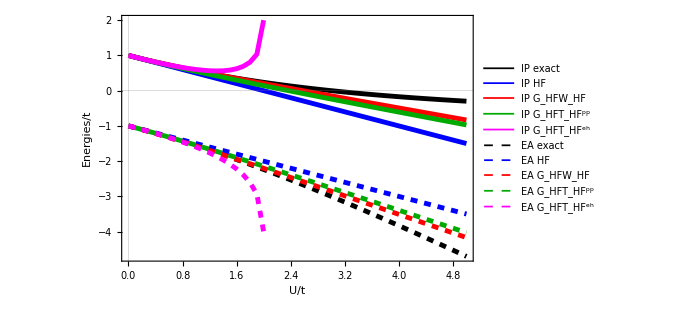

```mathematica
QPU=With[{t=1,Δv=0.0},ListPlot[
{Table[{U,ωEIexcas[t,U,Δv]},{U,0,5,0.1}],
Table[{U,-HubbardHF[t,U,Δv]⟦2,1⟧},{U,0,5,0.1}],
Table[{U,-HubbardGW[t,U,Δv]⟦3,1⟧},{U,0,5,0.1}],
Table[{U,-HubbardGT[t,U,Δv]⟦3,1⟧},{U,0,5,0.1}],
Table[{U,-HubbardGTehSpinOrb[t,U,Δv]⟦1,6,1⟧},{U,0,2.07,0.1}],
Table[{U,ωEAexcas[t,U,Δv]},{U,0,5,0.1}],
Table[{U,-HubbardHF[t,U,Δv]⟦2,2⟧},{U,0,5,0.1}],
Table[{U,-HubbardGW[t,U,Δv]⟦3,2⟧},{U,0,5,0.1}],
Table[{U,-HubbardGT[t,U,Δv]⟦3,2⟧},{U,0,5,0.1}],
Table[{U,-HubbardGTehSpinOrb[t,U,Δv]⟦1,6,2⟧},{U,0,2.07,0.1}]},
Joined->True,PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Magenta,Thickness[0.007]}},Frame->True,PlotLegends->{"IP exact","IP HF","IP G_HFW_HF","IP G_HFT_HF^pp","IP G_HFT_HF^eh","EA exact","EA HF","EA G_HFW_HF","EA G_HFT_HF^pp","EA G_HFT_HF^eh"},FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[Black,FontSize->20],FrameStyle->Directive[Black,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"
]] //Quiet
```

```mathematica
Export["qpU.pdf",QPU];
```

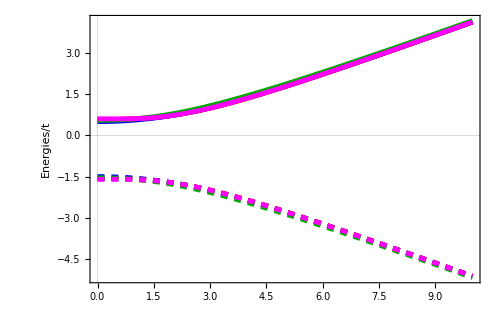

```mathematica
gr11=With[{t=1,U=1.0},ListPlot[
{Table[{Δv,ωEIexcas[t,U,Δv]},{Δv,0,10,0.1}],
Table[{Δv,-HubbardHF[t,U,Δv]⟦2,1⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGW[t,U,Δv]⟦3,1⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGT[t,U,Δv]⟦3,1⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGTehSpinOrb[t,U,Δv]⟦1,6,1⟧},{Δv,0,10,0.1}],
Table[{Δv,ωEAexcas[t,U,Δv]},{Δv,0,10,0.1}],
Table[{Δv,-HubbardHF[t,U,Δv]⟦2,2⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGW[t,U,Δv]⟦3,2⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGT[t,U,Δv]⟦3,2⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGTehSpinOrb[t,U,Δv]⟦1,6,2⟧},{Δv,0,10,0.1}]},
Joined->True,PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Magenta,Thickness[0.007]}},Frame->True,FrameLabel->{"","Energies/t"},LabelStyle->Directive[Black,FontSize->20],FrameStyle->Directive[Black,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"
]] //Quiet
```

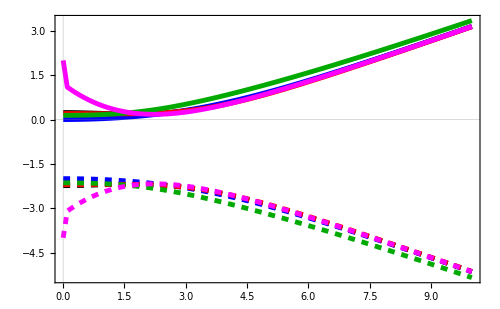

```mathematica
gr12=With[{t=1,U=2.0},ListPlot[
{Table[{Δv,ωEIexcas[t,U,Δv]},{Δv,0,10,0.1}],
Table[{Δv,-HubbardHF[t,U,Δv]⟦2,1⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGW[t,U,Δv]⟦3,1⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGT[t,U,Δv]⟦3,1⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGTehSpinOrb[t,U,Δv]⟦1,6,1⟧},{Δv,0,10,0.1}],
Table[{Δv,ωEAexcas[t,U,Δv]},{Δv,0,10,0.1}],
Table[{Δv,-HubbardHF[t,U,Δv]⟦2,2⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGW[t,U,Δv]⟦3,2⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGT[t,U,Δv]⟦3,2⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGTehSpinOrb[t,U,Δv]⟦1,6,2⟧},{Δv,0,10,0.1}]},
Joined->True,PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Magenta,Thickness[0.007]}},Frame->True,LabelStyle->Directive[Black,FontSize->20],FrameStyle->Directive[Black,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"
]] //Quiet
```

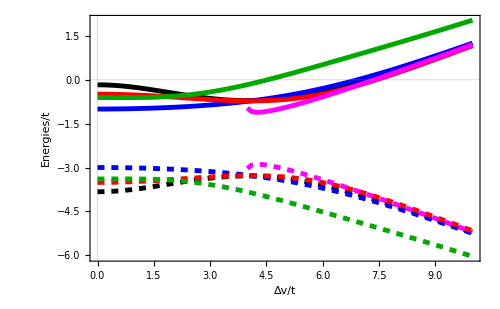

```mathematica
gr21=With[{t=1,U=4.0},ListPlot[
{Table[{Δv,ωEIexcas[t,U,Δv]},{Δv,0,10,0.1}],
Table[{Δv,-HubbardHF[t,U,Δv]⟦2,1⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGW[t,U,Δv]⟦3,1⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGT[t,U,Δv]⟦3,1⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGTehSpinOrb[t,U,Δv]⟦1,6,1⟧},{Δv,4,10,0.1}],
Table[{Δv,ωEAexcas[t,U,Δv]},{Δv,0,10,0.1}],
Table[{Δv,-HubbardHF[t,U,Δv]⟦2,2⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGW[t,U,Δv]⟦3,2⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGT[t,U,Δv]⟦3,2⟧},{Δv,0,10,0.1}],
Table[{Δv,-HubbardGTehSpinOrb[t,U,Δv]⟦1,6,2⟧},{Δv,4,10,0.1}]},
Joined->True,PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Magenta,Thickness[0.007]}},Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[Black,FontSize->20],FrameStyle->Directive[Black,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"
]] //Quiet
```

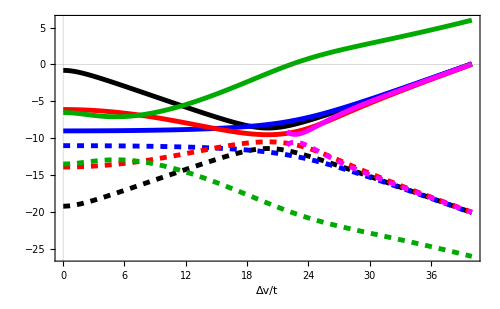

```mathematica
gr22=With[{t=1,U=20.0},ListPlot[
{Table[{Δv,ωEIexcas[t,U,Δv]},{Δv,0,40,0.1}],
Table[{Δv,-HubbardHF[t,U,Δv]⟦2,1⟧},{Δv,0,40,0.1}],
Table[{Δv,-HubbardGW[t,U,Δv]⟦3,1⟧},{Δv,0,40,0.1}],
Table[{Δv,-HubbardGT[t,U,Δv]⟦3,1⟧},{Δv,0,40,0.1}],
Table[{Δv,-HubbardGTehSpinOrb[t,U,Δv]⟦1,6,1⟧},{Δv,21.9,40,0.1}],
Table[{Δv,ωEAexcas[t,U,Δv]},{Δv,0,40,0.1}],
Table[{Δv,-HubbardHF[t,U,Δv]⟦2,2⟧},{Δv,0,40,0.1}],
Table[{Δv,-HubbardGW[t,U,Δv]⟦3,2⟧},{Δv,0,40,0.1}],
Table[{Δv,-HubbardGT[t,U,Δv]⟦3,2⟧},{Δv,0,40,0.1}],
Table[{Δv,-HubbardGTehSpinOrb[t,U,Δv]⟦1,6,2⟧},{Δv,21.9,40,0.1}]},
Joined->True,PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Magenta,Thickness[0.007]}},Frame->True,FrameLabel->{"Δv/t",""},LabelStyle->Directive[Black,FontSize->20],FrameStyle->Directive[Black,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"
]] //Quiet
```

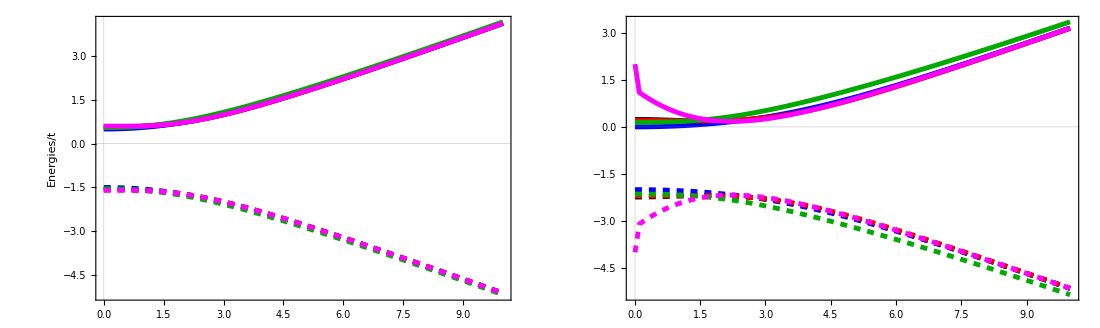

```mathematica
qp1=Legended[GraphicsGrid[{{gr11,gr12}},ImageSize->1100],LineLegend[{Black,Blue,Red,Darker[Green],Magenta,{Dashed,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Darker[Green]},{Dashed,Magenta}},{"IP exact","IP HF","IP G_HFW_HF","IP G_HFT_HF^pp","IP G_HFT_HF^eh","EA exact","EA HF","EA G_HFW_HF","EA G_HFT_HF^pp","EA G_HFT_HF^eh"},LabelStyle->Directive[FontFamily->"Arial",15]]]
```

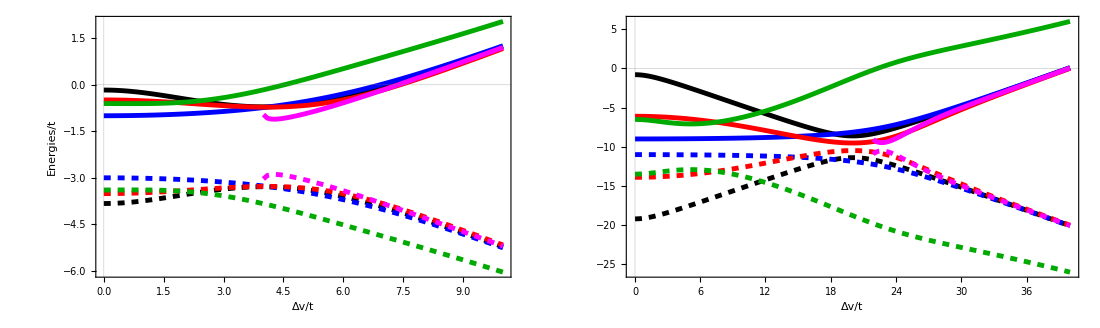

```mathematica
qp2=Legended[GraphicsGrid[{{gr21,gr22}},ImageSize->1100],LineLegend[{Black,Blue,Red,Darker[Green],Magenta,{Dashed,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Darker[Green]},{Dashed,Magenta}},{"IP exact","IP HF","IP G_HFW_HF","IP G_HFT_HF^pp","IP G_HFT_HF^eh","EA exact","EA HF","EA G_HFW_HF","EA G_HFT_HF^pp","EA G_HFT_HF^eh"},LabelStyle->Directive[FontFamily->"Arial",15]]]
```

```mathematica
FigsQP=GraphicsColumn[{qp1,qp2}]
```

-Graphics-

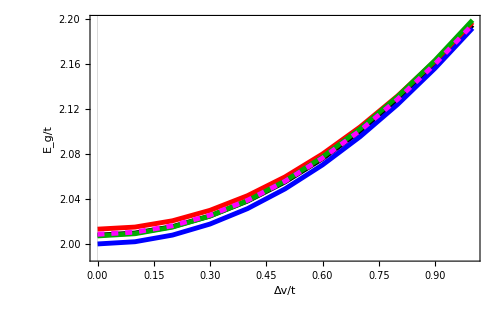

```mathematica
Gap1=With[{t=1.0,U=0.25},ListPlot[
{Table[{Δv,Egap[t,U,Δv]},{Δv,0,1,0.1}],
Table[{Δv,HubbardHF[t,U,Δv]⟦3⟧},{Δv,0,1,0.1}],
Table[{Δv,HubbardGW[t,U,Δv]⟦8⟧},{Δv,0,1,0.1}],
Table[{Δv,HubbardGT[t,U,Δv]⟦8⟧},{Δv,0,1,0.1}],
Table[{Δv,HubbardGTehSpinOrb[t,U,Δv]⟦1,1⟧},{Δv,0.0,1,0.1}]},
Joined->True,PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Magenta,Thickness[0.007]}},Frame->True,FrameLabel->{"Δv/t","E_g/t"},LabelStyle->Directive[Black,FontSize->20],FrameStyle->Directive[Black,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"]] //Quiet
```

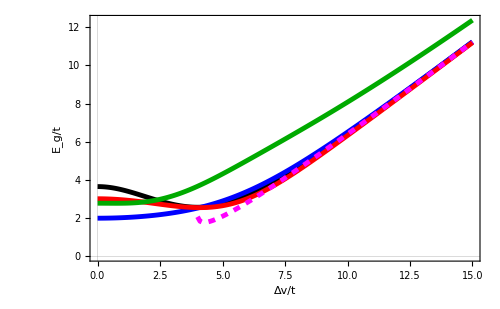

```mathematica
Gap2=With[{t=1.0,U=4},ListPlot[
{Table[{Δv,Egap[t,U,Δv]},{Δv,0,15,0.1}],
Table[{Δv,HubbardHF[t,U,Δv]⟦3⟧},{Δv,0,15,0.1}],
Table[{Δv,HubbardGW[t,U,Δv]⟦8⟧},{Δv,0,15,0.1}],
Table[{Δv,HubbardGT[t,U,Δv]⟦8⟧},{Δv,0,15,0.1}],
Table[{Δv,HubbardGTehSpinOrb[t,U,Δv]⟦1,1⟧},{Δv,4.0,15,0.1}]},
Joined->True,PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Magenta,Thickness[0.007]}},Frame->True,FrameLabel->{"Δv/t","E_g/t"},LabelStyle->Directive[Black,FontSize->20],FrameStyle->Directive[Black,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"]] //Quiet
```

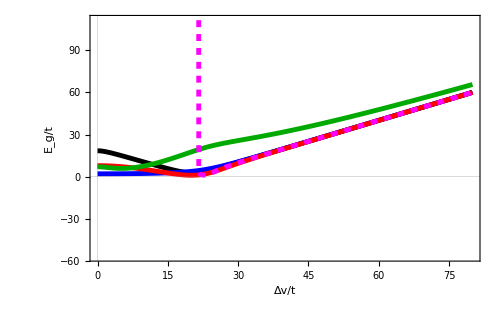

```mathematica
Gap3=With[{t=1.0,U=20.0},ListPlot[
{Table[{Δv,Egap[t,U,Δv]},{Δv,0,80,0.1}],
Table[{Δv,HubbardHF[t,U,Δv]⟦3⟧},{Δv,0,80,0.1}],
Table[{Δv,HubbardGW[t,U,Δv]⟦8⟧},{Δv,0,80,0.1}],
Table[{Δv,HubbardGT[t,U,Δv]⟦8⟧},{Δv,0,80,0.1}],
Table[{Δv,HubbardGTehSpinOrb[t,U,Δv]⟦1,1⟧},{Δv,20.0,80,0.1}]},
Joined->True,PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Magenta,Thickness[0.007]}},Frame->True,FrameLabel->{"Δv/t","E_g/t"},LabelStyle->Directive[Black,FontSize->20],FrameStyle->Directive[Black,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"]] //Quiet
```

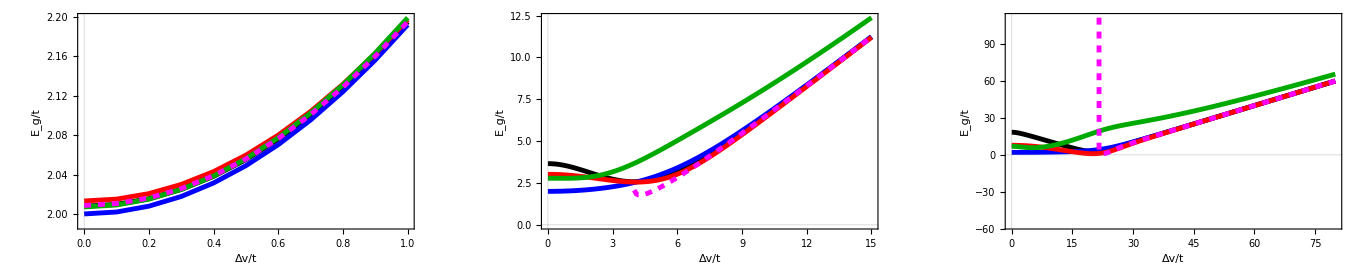

```mathematica
EG=Legended[GraphicsGrid[{{Gap1,Gap2,Gap3}},ImageSize->Full],LineLegend[{Black,Blue,Red,Darker[Green],Magenta},{"E_g exact","E_g HF","E_g G_HFW_HF","E_g G_HFT_HF^pp","E_g G_HFT_HF^eh"},LabelStyle->Directive[FontFamily->"Arial",20]]]
```

#### Courbes Excitations neutres

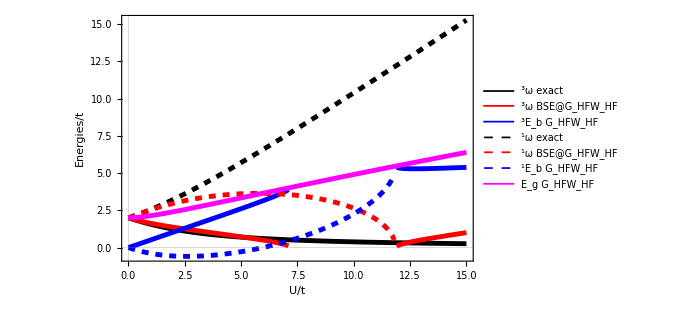

```mathematica
TripletSinguletGW=With[{t=1.0,Δv=0.0},ListPlot[
{Table[Flatten[{U,excas1[t,U,Δv]}],{U,0,15,0.1}],
Table[Flatten[{U,BSE[t,U,Δv][[1,2]]}],{U,0,15,0.1}],
Table[Flatten[{U,BSE[t,U,Δv][[1,3]]}],{U,0,15,0.1}],
Table[Flatten[{U,excas2[t,U,Δv]}],{U,0,15,0.1}],
Table[Flatten[{U,BSE[t,U,Δv][[2,2]]}],{U,0,15,0.1}],
Table[Flatten[{U,BSE[t,U,Δv][[2,3]]}],{U,0,15,0.1}],
Table[Flatten[{U,BSE[t,U,Δv][[1,1]]}],{U,0,15,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@G_HFW_HF","^3E_b G_HFW_HF","^1ω exact","^1ω BSE@G_HFW_HF","^1E_b G_HFW_HF"," E_g G_HFW_HF"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Red,Thickness[0.007]},{Blue,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Magenta,Thickness[0.007]}}
]] //Quiet
```

```mathematica
Export["Excitations_neutres_GAP_Eb_GW.pdf",TripletSinguletGW];
```

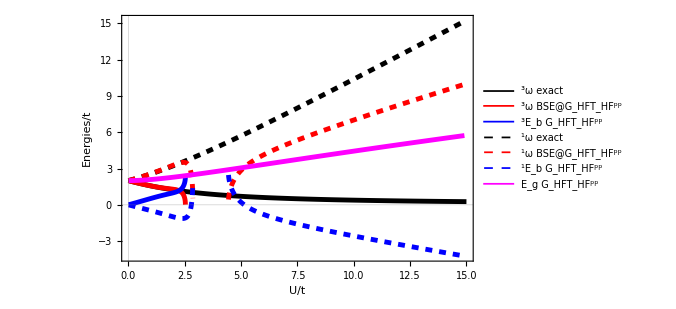

```mathematica
TripletSinguletGT=With[{t=1.0,Δv=0.0},ListPlot[
{Table[Flatten[{U,excas1[t,U,Δv]}],{U,0,15,0.1}],
Table[Flatten[{U,BSEGTαβ[t,U,Δv][[1,2]]}],{U,0.01,15,0.01}],
Table[Flatten[{U,BSEGTαβ[t,U,Δv][[1,3]]}],{U,0.01,15,0.01}],
Table[Flatten[{U,excas2[t,U,Δv]}],{U,0,15,0.1}],
Table[Flatten[{U,BSEGTαβ[t,U,Δv][[2,2]]}],{U,0.01,15,0.01}],
Table[Flatten[{U,BSEGTαβ[t,U,Δv][[2,3]]}],{U,0.01,15,0.01}],
Table[Flatten[{U,BSEGTαβ[t,U,Δv][[1,1]]}],{U,0.01,15,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@G_HFT_HF^pp","^3E_b G_HFT_HF^pp","^1ω exact","^1ω BSE@G_HFT_HF^pp","^1E_b G_HFT_HF^pp"," E_g G_HFT_HF^pp"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Red,Thickness[0.007]},{Blue,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Magenta,Thickness[0.007]}}
]] //Quiet
```

```mathematica
Export["Excitations_neutres_GAP_Eb_OppGHF.pdf",TripletSinguletGT];
```

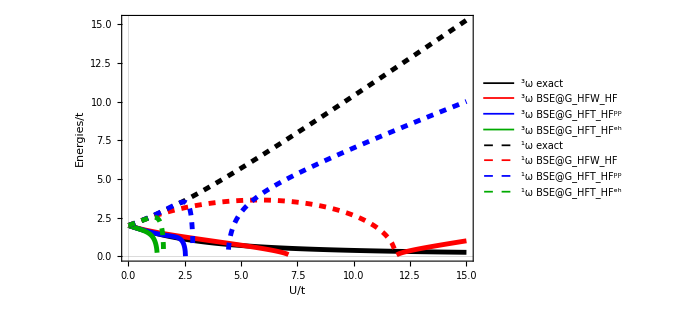

```mathematica
excneutres=With[{t=1.0,Δv=0.0},ListPlot[
{Table[Flatten[{U,excas1[t,U,Δv]}],{U,0,15,0.1}],
Table[Flatten[{U,BSE[t,U,Δv][[1,2]]}],{U,0,15,0.1}],
Table[Flatten[{U,BSEGTαβ[t,U,Δv][[1,2]]}],{U,0.01,15,0.01}],
Table[Flatten[{U,HubbardGTehSpinOrb[t,U,0.0][[1,2]]}],{U,0,1.95,0.01}],
Table[Flatten[{U,excas2[t,U,Δv]}],{U,0,15,0.1}],
Table[Flatten[{U,BSE[t,U,Δv][[2,2]]}],{U,0,15,0.1}],
Table[Flatten[{U,BSEGTαβ[t,U,Δv][[2,2]]}],{U,0.01,15,0.01}],
Table[Flatten[{U,HubbardGTehSpinOrb[t,U,0.0][[2,2]]}],{U,0,1.95,0.01}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@G_HFW_HF","^3ω BSE@G_HFT_HF^pp","^3ω BSE@G_HFT_HF^eh","^1ω exact","^1ω BSE@G_HFW_HF","^1ω BSE@G_HFT_HF^pp","^1ω BSE@G_HFT_HF^eh"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Red,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]}}
]] //Quiet
```

```mathematica
Export["excitations_neutres_dim_sym.pdf",excneutres];
```

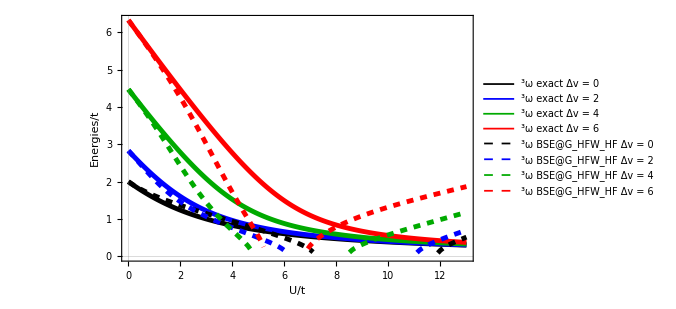

```mathematica
im1=With[{t=1.0},ListPlot[
{Table[Flatten[{U,excas1[t,U,0.0]}],{U,0,13,0.1}],
Table[Flatten[{U,excas1[t,U,2.]}],{U,0,13,0.1}],
Table[Flatten[{U,excas1[t,U,4.]}],{U,0,13,0.1}],
Table[Flatten[{U,excas1[t,U,6.]}],{U,0,13,0.1}],
Table[Flatten[{U,BSE[t,U,0.][[1,2]]}],{U,0,13,0.1}],
Table[Flatten[{U,BSE[t,U,2.][[1,2]]}],{U,0,13,0.1}],
Table[Flatten[{U,BSE[t,U,4.][[1,2]]}],{U,0,13,0.1}],
Table[Flatten[{U,BSE[t,U,6.][[1,2]]}],{U,0,13,0.1}]},
Joined->True,PlotLegends->{"^3ω exact Δv = 0","^3ω exact Δv = 2","^3ω exact Δv = 4","^3ω exact Δv = 6","^3ω BSE@G_HFW_HF Δv = 0","^3ω BSE@G_HFW_HF Δv = 2","^3ω BSE@G_HFW_HF Δv = 4","^3ω BSE@G_HFW_HF Δv = 6"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Red,Thickness[0.007]}}
]] //Quiet
```

```mathematica
Export["w1_U_BSEGW_as.png",im1];
```

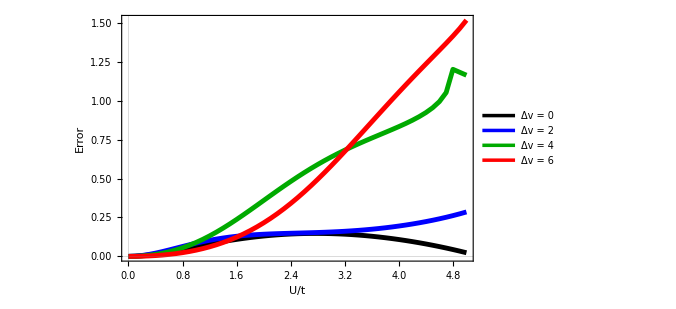

```mathematica
im2=With[{t=1.0},ListPlot[
{Table[Flatten[{U,Abs[BSE[t,U,0.][[1,2]]-excas1[t,U,0.0]]}],{U,0,5,0.1}],
Table[Flatten[{U,Abs[BSE[t,U,2.][[1,2]]-excas1[t,U,2.]]}],{U,0,5,0.1}],
Table[Flatten[{U,Abs[BSE[t,U,4.][[1,2]]-excas1[t,U,4.]]}],{U,0,5,0.1}],
Table[Flatten[{U,Abs[BSE[t,U,6.][[1,2]]-excas1[t,U,6.]]}],{U,0,5,0.1}]},
Joined->True,PlotLegends->{"Δv = 0","Δv = 2","Δv = 4","Δv = 6"},Frame->True,FrameLabel->{"U/t","Error"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Red,Thickness[0.007]}}
]] //Quiet
```

```mathematica
Export["err_w1_BSEGW_as.png",im2];
```

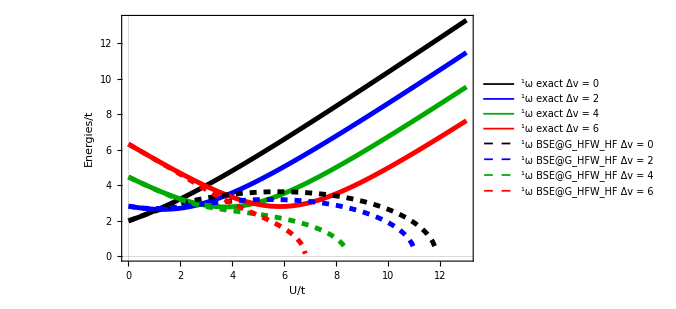

```mathematica
im3=With[{t=1.0},ListPlot[
{Table[Flatten[{U,excas2[t,U,0.0]}],{U,0,13,0.1}],
Table[Flatten[{U,excas2[t,U,2.]}],{U,0,13,0.1}],
Table[Flatten[{U,excas2[t,U,4.]}],{U,0,13,0.1}],
Table[Flatten[{U,excas2[t,U,6.]}],{U,0,13,0.1}],
Table[Flatten[{U,BSE[t,U,0.][[2,2]]}],{U,0,13,0.1}],
Table[Flatten[{U,BSE[t,U,2.][[2,2]]}],{U,0,13,0.1}],
Table[Flatten[{U,BSE[t,U,4.][[2,2]]}],{U,0,13,0.1}],
Table[Flatten[{U,BSE[t,U,6.][[2,2]]}],{U,0,13,0.1}]},
Joined->True,PlotLegends->{"^1ω exact Δv = 0","^1ω exact Δv = 2","^1ω exact Δv = 4","^1ω exact Δv = 6","^1ω BSE@G_HFW_HF Δv = 0","^1ω BSE@G_HFW_HF Δv = 2","^1ω BSE@G_HFW_HF Δv = 4","^1ω BSE@G_HFW_HF Δv = 6"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Red,Thickness[0.007]}}
]] //Quiet
```

```mathematica
Export["w2_U_BSEGW_as.png",im3];
```

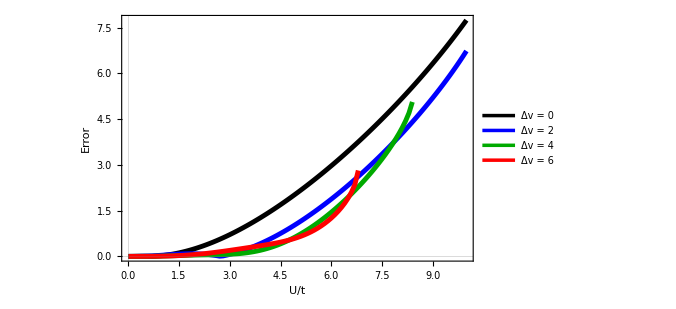

```mathematica
im4=With[{t=1.0},ListPlot[
{Table[Flatten[{U,Abs[BSE[t,U,0.][[2,2]]-excas2[t,U,0.0]]}],{U,0,10,0.1}],
Table[Flatten[{U,Abs[BSE[t,U,2.][[2,2]]-excas2[t,U,2.]]}],{U,0,10,0.1}],
Table[Flatten[{U,Abs[BSE[t,U,4.][[2,2]]-excas2[t,U,4.]]}],{U,0,10,0.1}],
Table[Flatten[{U,Abs[BSE[t,U,6.][[2,2]]-excas2[t,U,6.]]}],{U,0,10,0.1}]},
Joined->True,PlotLegends->{"Δv = 0","Δv = 2","Δv = 4","Δv = 6"},Frame->True,FrameLabel->{"U/t","Error"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Red,Thickness[0.007]}}
]] //Quiet
```

```mathematica
Export["err_w2_BSEGW_as.png",im4];
```

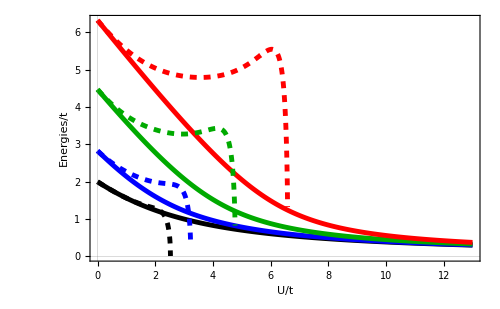

```mathematica
imGT1=With[{t=1.0},ListPlot[
{Table[Flatten[{U,excas1[t,U,0.0]}],{U,0,13,0.1}],
Table[Flatten[{U,excas1[t,U,2.]}],{U,0,13,0.1}],
Table[Flatten[{U,excas1[t,U,4.]}],{U,0,13,0.1}],
Table[Flatten[{U,excas1[t,U,6.]}],{U,0,13,0.1}],
Table[Flatten[{U,BSEGTαβ[t,U,0.][[1,2]]}],{U,0.01,13,0.01}],
Table[Flatten[{U,BSEGTαβ[t,U,2.][[1,2]]}],{U,0.01,13,0.01}],
Table[Flatten[{U,BSEGTαβ[t,U,4.][[1,2]]}],{U,0.01,13,0.01}],
Table[Flatten[{U,BSEGTαβ[t,U,6.][[1,2]]}],{U,0.01,13,0.01}]},
Joined->True,Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Red,Thickness[0.007]}}
]] //Quiet
```

```mathematica
Export["w1_U_BSEGT_as.png",imGT1];
```

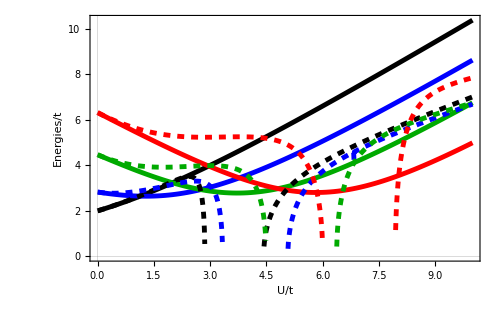

```mathematica
imGT2=With[{t=1.0},ListPlot[
{Table[Flatten[{U,excas2[t,U,0.0]}],{U,0,10,0.1}],
Table[Flatten[{U,excas2[t,U,2.]}],{U,0,10,0.1}],
Table[Flatten[{U,excas2[t,U,4.]}],{U,0,10,0.1}],
Table[Flatten[{U,excas2[t,U,6.]}],{U,0,10,0.1}],
Table[Flatten[{U,BSEGTαβ[t,U,0.][[2,2]]}],{U,0.01,10,0.01}],
Table[Flatten[{U,BSEGTαβ[t,U,2.][[2,2]]}],{U,0.01,10,0.01}],
Table[Flatten[{U,BSEGTαβ[t,U,4.][[2,2]]}],{U,0.01,10,0.01}],
Table[Flatten[{U,BSEGTαβ[t,U,6.][[2,2]]}],{U,0.01,10,0.01}]},
Joined->True,Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Red,Thickness[0.007]}}
]] //Quiet
```

```mathematica
Export["w2_U_BSEGT_as.png",imGT2];
```

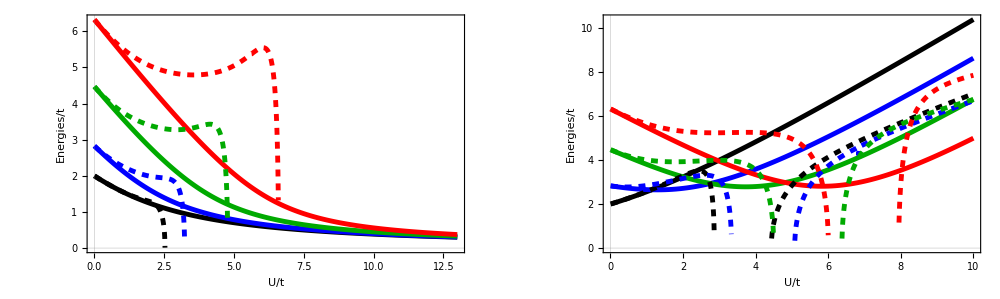

```mathematica
ωBSEGTU=Legended[GraphicsGrid[{{imGT1,imGT2}},ImageSize->1000],LineLegend[{{Dashed,Black},{Dashed,RGBColor[0.365248, 0.427802, 0.758297]},{Dashed,RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023]},{Dashed,Red},Black,RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],Red},{"BSE@G_HFT_HF^pp Δv = 0","ω BSE@G_HFT_HF^pp Δv = 2","ω BSE@G_HFT_HF^pp Δv = 4","ω BSE@G_HFT_HF^pp Δv = 6","Exact Δv = 0","Exact Δv = 2","Exact Δv = 4","Exact Δv = 6"}]]
```

```mathematica
Export["w_U_BSEGT_as.png",ωBSEGTU];
```

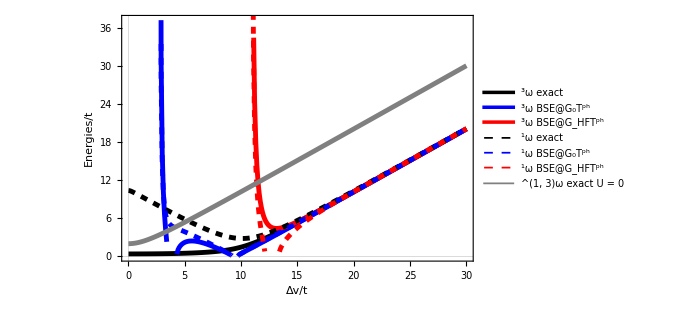

```mathematica
Show[i1,i2,i3,i4]
```

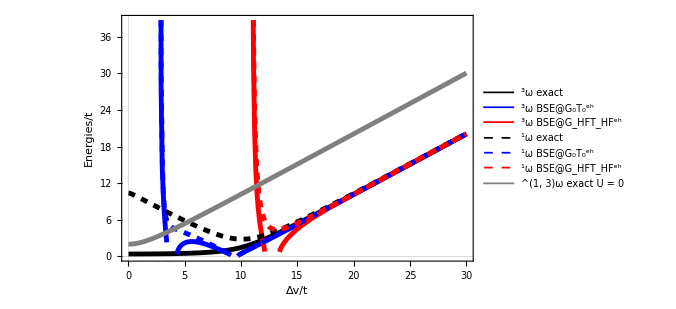

```mathematica
BSETphωGzGhfDv=With[{t=N[1,200],U=N[10,200]},
ListPlot[
{Table[Flatten[{Δv,excas1[t,U,Δv]}],{Δv,0,30,0.1}],
BSETphGzωtriplet,
Table[Flatten[{Δv,HubbardGTehSpinOrb[t,U,Δv][[1,2]]}],{Δv,11,30,0.1}],
Table[Flatten[{Δv,excas2[t,U,Δv]}],{Δv,0,30,0.1}],
BSETphGzωsingulet,
Table[Flatten[{Δv,HubbardGTehSpinOrb[t,U,Δv][[2,2]]}],{Δv,11,30,0.1}],
Table[Flatten[{Δv,excas1[t,0,Δv]}],{Δv,0,30,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@G_0T_0^eh","^3ω BSE@G_HFT_HF^eh","^1ω exact","^1ω BSE@G_0T_0^eh","^1ω BSE@G_HFT_HF^eh","^(1, 3)ω exact U = 0"},Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Gray,Thickness[0.007]}}]]//Quiet
```

```mathematica
Export["BSEwTphGzGhfDv.pdf",BSETphωGzGhfDv];
```

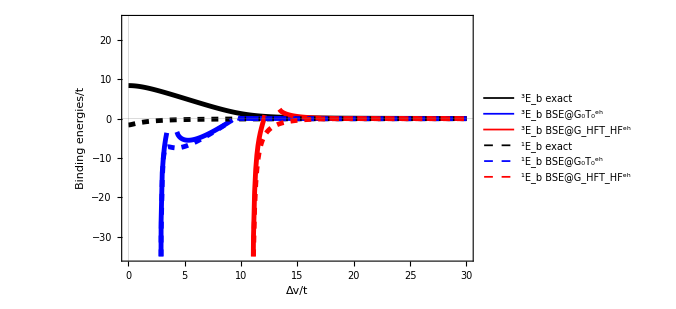

```mathematica
BSETphEbGzGhfDv=With[{t=N[1,150],U=N[10,150]},ListPlot[
{Table[Flatten[{Δv,Eb1exc[t,U,Δv]}],{Δv,0,30,0.1}],
BSETphGzEbtriplet,
Table[Flatten[{Δv,HubbardGTehSpinOrb[t,U,Δv][[1,3]]}],{Δv,11,30,0.1}],
Table[Flatten[{Δv,Eb2exc[t,U,Δv]}],{Δv,0,30,0.1}],
BSETphGzEbsingulet,
Table[Flatten[{Δv,HubbardGTehSpinOrb[t,U,Δv][[2,3]]}],{Δv,11,30,0.1}]},
Joined->True,PlotRange->{{0,30},{-35,25}},PlotLegends->{"^3E_b exact","^3E_b BSE@G_0T_0^eh","^3E_b BSE@G_HFT_HF^eh","^1E_b exact","^1E_b BSE@G_0T_0^eh","^1E_b BSE@G_HFT_HF^eh"},Frame->True,FrameLabel->{"Δv/t","Binding energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Red,Thickness[0.007]}}]]//Quiet
```

```mathematica
Export["BSEEbTphGzGhfDv.pdf",BSETphEbGzGhfDv];
```

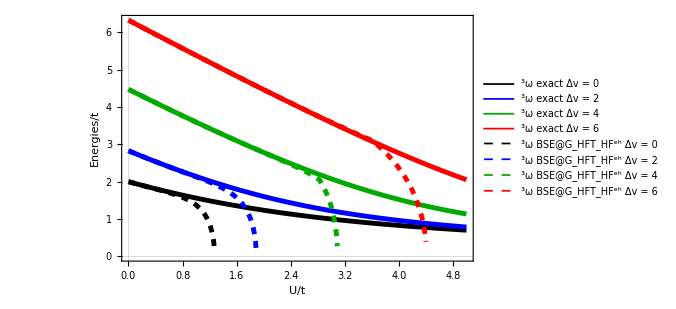

```mathematica
BSETphωtriplet=With[{t=N[1,150]},ListPlot[
{Table[{U,excas1[t,U,0.0]},{U,0,5,0.1}],
Table[{U,excas1[t,U,2.0]},{U,0,5,0.1}],
Table[{U,excas1[t,U,4.0]},{U,0,5,0.1}],
Table[{U,excas1[t,U,6.0]},{U,0,5,0.1}],
Table[{U,HubbardGTehSpinOrb[t,U,0.0]⟦1,2⟧},{U,0,N[2,150],0.01}],
Table[{U,HubbardGTehSpinOrb[t,U,2.0]⟦1,2⟧},{U,0,N[2,150],0.01}],
Table[{U,HubbardGTehSpinOrb[t,U,4.0]⟦1,2⟧},{U,0,N[4,150],0.01}],
Table[{U,HubbardGTehSpinOrb[t,U,6.0]⟦1,2⟧},{U,0,N[5,150],0.01}]
},
Joined->True,PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Red,Thickness[0.007]}},Frame->True,PlotLegends->{"^3ω exact Δv = 0","^3ω exact Δv = 2","^3ω exact Δv = 4","^3ω exact Δv = 6","^3ω BSE@G_HFT_HF^eh Δv = 0","^3ω BSE@G_HFT_HF^eh Δv = 2","^3ω BSE@G_HFT_HF^eh Δv = 4","^3ω BSE@G_HFT_HF^eh Δv = 6"},FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[Black,FontSize->20],FrameStyle->Directive[Black,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"
]] //Quiet
```

```mathematica
Export["BSETph_w_triplet_plusieurs_Dv.pdf",BSETphωtriplet];
```

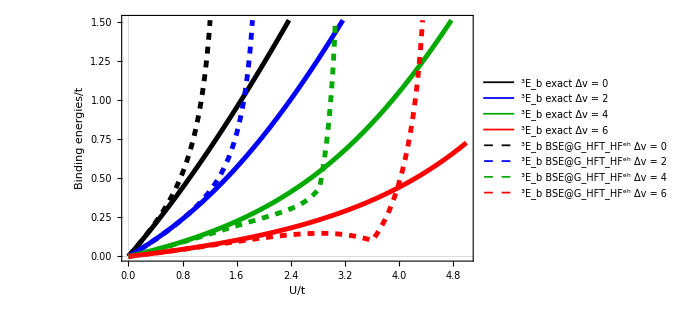

```mathematica
BSETphEbtriplet=With[{t=N[1,150]},ListPlot[
{Table[{U,Eb1exc[t,U,0.0]},{U,0,5,0.1}],
Table[{U,Eb1exc[t,U,2.0]},{U,0,5,0.1}],
Table[{U,Eb1exc[t,U,4.0]},{U,0,5,0.1}],
Table[{U,Eb1exc[t,U,6.0]},{U,0,5,0.1}],
Table[{U,HubbardGTehSpinOrb[t,U,0.0]⟦1,3⟧},{U,0,N[2.0,150],0.01}],
Table[{U,HubbardGTehSpinOrb[t,U,2.0]⟦1,3⟧},{U,0,N[2.0,150],0.01}],
Table[{U,HubbardGTehSpinOrb[t,U,4.0]⟦1,3⟧},{U,0,N[4.0,150],0.01}],
Table[{U,HubbardGTehSpinOrb[t,U,6.0]⟦1,3⟧},{U,0,N[5,150],0.01}]
},
Joined->True,PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Red,Thickness[0.007]}},Frame->True,PlotLegends->{"^3E_b exact Δv = 0","^3E_b exact Δv = 2","^3E_b exact Δv = 4","^3E_b exact Δv = 6","^3E_b BSE@G_HFT_HF^eh Δv = 0","^3E_b BSE@G_HFT_HF^eh Δv = 2","^3E_b BSE@G_HFT_HF^eh Δv = 4","^3E_b BSE@G_HFT_HF^eh Δv = 6"},FrameLabel->{"U/t","Binding energies/t"},LabelStyle->Directive[Black,FontSize->20],FrameStyle->Directive[Black,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"
]] //Quiet
```

```mathematica
Export["BSETph_Eb_triplet_plusieurs_Dv.pdf",BSETphEbtriplet];
```

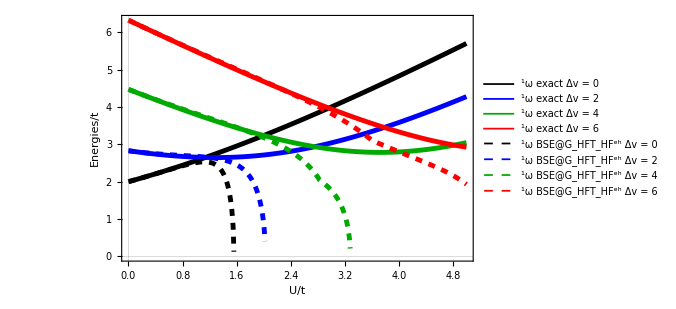

```mathematica
bseTphωsingulet=With[{t=N[1,150]},ListPlot[
{Table[{U,excas2[t,U,0.0]},{U,0,5,0.1}],
Table[{U,excas2[t,U,2.0]},{U,0,5,0.1}],
Table[{U,excas2[t,U,4.0]},{U,0,5,0.1}],
Table[{U,excas2[t,U,6.0]},{U,0,5,0.1}],
Table[{U,HubbardGTehSpinOrb[t,U,0.0]⟦2,2⟧},{U,0,N[2,150],0.01}],
Table[{U,HubbardGTehSpinOrb[t,U,2.0]⟦2,2⟧},{U,0,N[2.2,150],0.01}],
Table[{U,HubbardGTehSpinOrb[t,U,4.0]⟦2,2⟧},{U,0,N[3.5,150],0.01}],
Table[{U,HubbardGTehSpinOrb[t,U,6.0]⟦2,2⟧},{U,0,N[5,150],0.01}]
},
Joined->True,PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Red,Thickness[0.007]}},Frame->True,PlotLegends->{"^1ω exact Δv = 0","^1ω exact Δv = 2","^1ω exact Δv = 4","^1ω exact Δv = 6","^1ω BSE@G_HFT_HF^eh Δv = 0","^1ω BSE@G_HFT_HF^eh Δv = 2","^1ω BSE@G_HFT_HF^eh Δv = 4","^1ω BSE@G_HFT_HF^eh Δv = 6"},FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[Black,FontSize->20],FrameStyle->Directive[Black,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"
]] //Quiet
```

```mathematica
Export["BSETph_w_singulet_plusieurs_Dv.pdf",bseTphωsingulet];
```

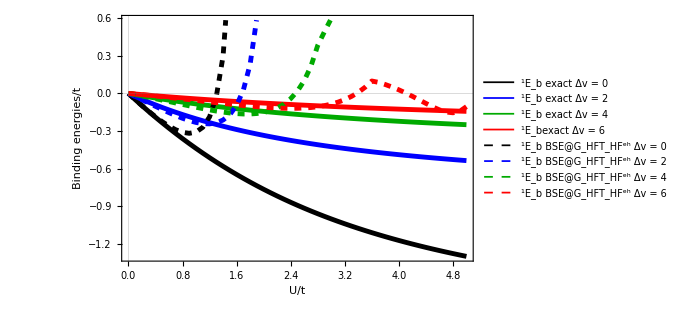

```mathematica
EbTphωsingulet=With[{t=N[1,150]},ListPlot[
{Table[{U,Eb2exc[t,U,0.0]},{U,0,5,0.1}],
Table[{U,Eb2exc[t,U,2.0]},{U,0,5,0.1}],
Table[{U,Eb2exc[t,U,4.0]},{U,0,5,0.1}],
Table[{U,Eb2exc[t,U,6.0]},{U,0,5,0.1}],
Table[{U,HubbardGTehSpinOrb[t,U,0.0]⟦2,3⟧},{U,0,N[2,150],0.1}],
Table[{U,HubbardGTehSpinOrb[t,U,2.0]⟦2,3⟧},{U,0,N[2.2,150],0.1}],
Table[{U,HubbardGTehSpinOrb[t,U,4.0]⟦2,3⟧},{U,0,N[3.5,150],0.1}],
Table[{U,HubbardGTehSpinOrb[t,U,6.0]⟦2,3⟧},{U,0,N[5,150],0.1}]
},
Joined->True,PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Red,Thickness[0.007]}},Frame->True,PlotLegends->{"^1E_b exact Δv = 0","^1E_b exact Δv = 2","^1E_b exact Δv = 4","^1E_bexact Δv = 6","^1E_b BSE@G_HFT_HF^eh Δv = 0","^1E_b BSE@G_HFT_HF^eh Δv = 2","^1E_b BSE@G_HFT_HF^eh Δv = 4","^1E_b BSE@G_HFT_HF^eh Δv = 6"},FrameLabel->{"U/t","Binding energies/t"},LabelStyle->Directive[Black,FontSize->20],FrameStyle->Directive[Black,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"
]] //Quiet
```

```mathematica
Export["BSETph_Eb_singulet_plusieurs_Dv.pdf",EbTphωsingulet];
```

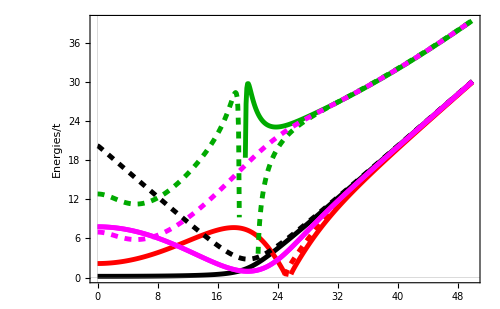

```mathematica
im11=With[{t=1.0,U=20.0},ListPlot[
{Table[Flatten[{Δv,excas1[t,U,Δv]}],{Δv,0,50,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[1,2]]}],{Δv,0,50,0.1}],
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[1,2]]}],{Δv,0.01,50,0.1}],
Table[Flatten[{Δv,excas2[t,U,Δv]}],{Δv,0,50,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[2,2]]}],{Δv,0,50,0.1}],
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[2,2]]}],{Δv,0.01,50,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[1,1]]}],{Δv,0,50,0.1}],
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[1,1]]}],{Δv,0.01,50,0.1}],
Table[{Δv,BSE[t,U,Δv][[1,1]]},{Δv,0,50,0.1}]},
Joined->True,Frame->True,FrameLabel->{"","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]},{Dashed,Magenta,Thickness[0.007]},{Magenta,Thickness[0.007]}}
]]  //Quiet
```

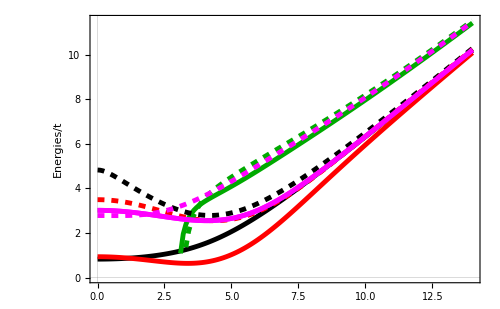

```mathematica
im12=With[{t=1.0,U=4.0},ListPlot[
{Table[Flatten[{Δv/t,excas1[t,U,Δv]/t}],{Δv,0,14,0.1}],
Table[Flatten[{Δv/t,BSE[t,U,Δv][[1,2]]/t}],{Δv,0,14,0.1}],
Table[Flatten[{Δv/t,BSEGTαβ[t,U,Δv][[1,2]]/t}],{Δv,0,14,0.1}],
Table[Flatten[{Δv/t,excas2[t,U,Δv]/t}],{Δv,0,14,0.1}],
Table[Flatten[{Δv/t,BSE[t,U,Δv][[2,2]]/t}],{Δv,0,14,0.1}],
Table[Flatten[{Δv/t,BSEGTαβ[t,U,Δv][[2,2]]/t}],{Δv,0,14,0.1}],
Table[Flatten[{Δv/t,BSE[t,U,Δv][[1,1]]/t}],{Δv,0,14,0.1}],
Table[Flatten[{Δv/t,BSEGTαβ[t,U,Δv][[1,1]]/t}],{Δv,0,14,0.1}],
Table[{Δv/t,BSE[t,U,Δv][[1,1]]/t},{Δv,0,14,0.1}]},
Joined->True,Frame->True,FrameLabel->{"","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]},{Dashed,Magenta,Thickness[0.007]},{Magenta,Thickness[0.007]}}
]]  //Quiet
```

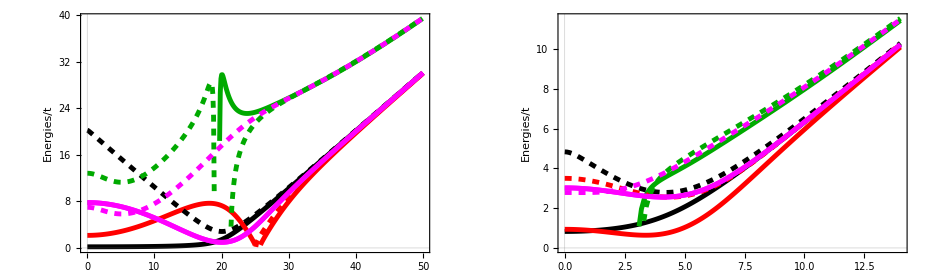

```mathematica
Excneutres=Legended[GraphicsGrid[{{im11,im12}},ImageSize->925],LineLegend[{Black,Red,Darker[Green],{Dashed,Black},{Dashed,Red},{Dashed,Darker[Green]},Magenta,{Dashed,Magenta},Magenta},{"^3ω exact","^3ω BSE@G_HFW_HF","^3ω BSE@G_HFT_HF^pp","^1ω exact singlet","^1ω BSE@G_HFW_HF","^1ω BSE@G_HFT_HF^pp","E_g G_HFW_HF","E_g G_HFT_HF^pp"},LabelStyle->Directive[FontFamily->"Arial",20]]]
```

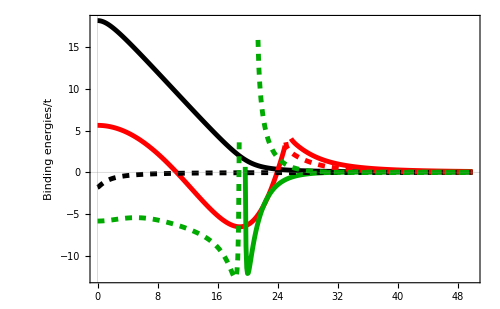

```mathematica
imEb1=With[{t=1.0,U=20.0},ListPlot[
{Table[Flatten[{Δv/t,Eb1exc[t,U,Δv]/t}],{Δv,0,50,0.1}],
Table[Flatten[{Δv/t,BSE[t,U,Δv][[1,3]]/t}],{Δv,0,50,0.1}],
Table[Flatten[{Δv/t,BSEGTαβ[t,U,Δv][[1,3]]/t}],{Δv,0,50,0.1}],
Table[Flatten[{Δv/t,Eb2exc[t,U,Δv]/t}],{Δv,0,50,0.1}],
Table[Flatten[{Δv/t,BSE[t,U,Δv][[2,3]]/t}],{Δv,0,50,0.1}],
Table[Flatten[{Δv/t,BSEGTαβ[t,U,Δv][[2,3]]/t}],{Δv,0,50,0.1}]},
Joined->True,Frame->True,FrameLabel->{"","Binding energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific", PlotRange->All, PlotStyle->{{Black,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]}}
]]  //Quiet
```

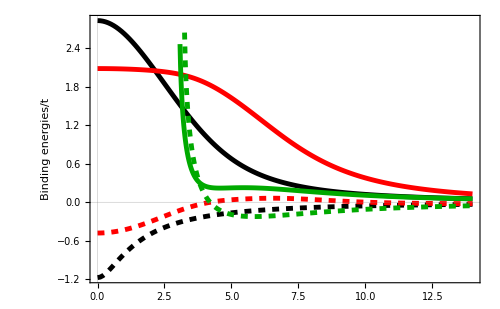

```mathematica
imEb2=With[{t=1.0,U=4.0},ListPlot[
{Table[Flatten[{Δv/t,Eb1exc[t,U,Δv]/t}],{Δv,0,14,0.1}],
Table[Flatten[{Δv/t,BSE[t,U,Δv][[1,3]]/t}],{Δv,0,14,0.1}],
Table[Flatten[{Δv/t,BSEGTαβ[t,U,Δv][[1,3]]/t}],{Δv,0,14,0.020}],
Table[Flatten[{Δv/t,Eb2exc[t,U,Δv]/t}],{Δv,0,14,0.1}],
Table[Flatten[{Δv/t,BSE[t,U,Δv][[2,3]]/t}],{Δv,0,14,0.1}],
Table[Flatten[{Δv/t,BSEGTαβ[t,U,Δv][[2,3]]/t}],{Δv,0,14,0.025}]},
Joined->True,Frame->True,FrameLabel->{"","Binding energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotRange->All, PlotStyle->{{Black,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]}}
]]  //Quiet
```

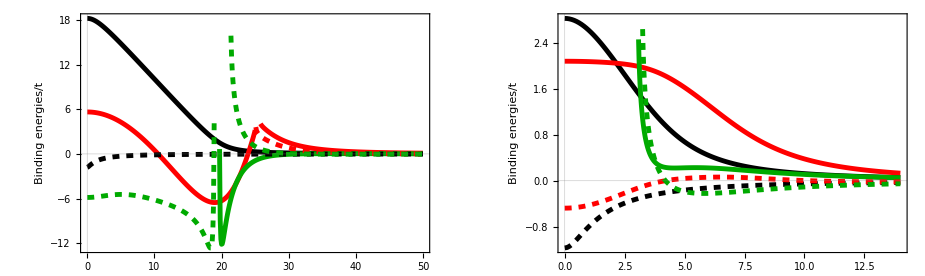

```mathematica
Eb=Legended[GraphicsGrid[{{imEb1,imEb2}},ImageSize->925],LineLegend[{Black,Red,Darker[Green],{Dashed,Black},{Dashed,Red},{Dashed,Darker[Green]}},{"^3E_b exact","^3E_b BSE@G_HFW_HF","^3E_b BSE@G_HFT_HF^pp","^1E_b exact ","^1E_b BSE@G_HFW_HF","^1E_b BSE@G_HFT_HF^pp"},LabelStyle->Directive[FontFamily->"Arial",20]]]
```

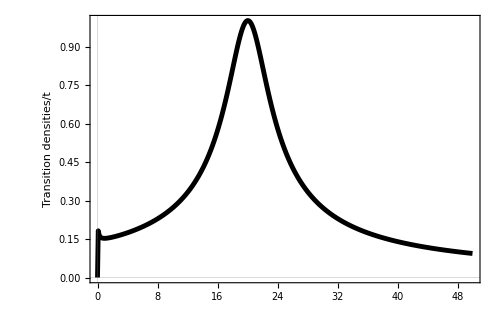

```mathematica
im31=With[{t=1.0,U=20.0},ListPlot[
{Table[Flatten[{Δv/t,Densite[t,U,Δv][[5]]-Densite[t,U,Δv][[6]]}],{Δv,0.0,50,0.1}]},
Joined->True,Frame->True,FrameLabel->{"","Transition densities/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotRange->All, PlotStyle->{{Black,Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]}}
]]  //Quiet
```

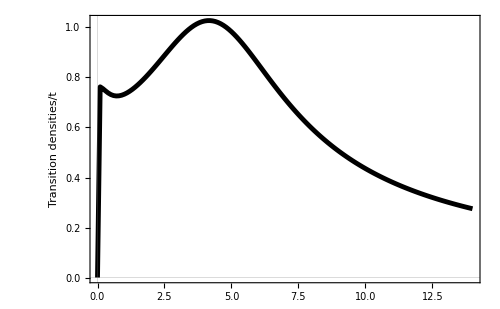

```mathematica
im32=With[{t=1.0,U=4.0},ListPlot[
{Table[Flatten[{Δv/t,Densite[t,U,Δv][[5]]-Densite[t,U,Δv][[6]]}],{Δv,0.0,14,0.1}]},
Joined->True,Frame->True,FrameLabel->{"","Transition densities/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotRange->All, PlotStyle->{{Black,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]}}
]]  //Quiet
```

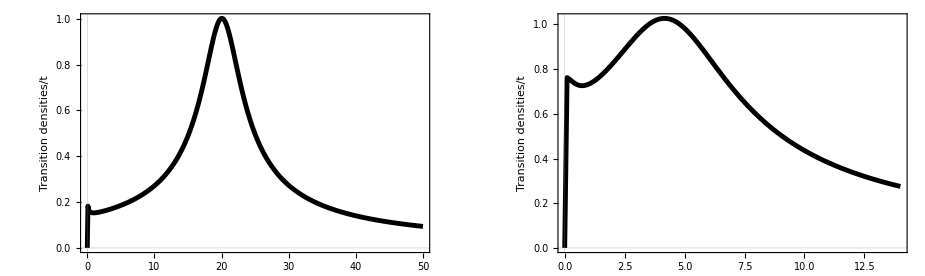

```mathematica
d=Legended[GraphicsGrid[{{im31,im32}},ImageSize->925],LineLegend[{Black,White},{"f_1 exact","                              "} ,LabelStyle->Directive[FontFamily->"Arial",20]]]
```

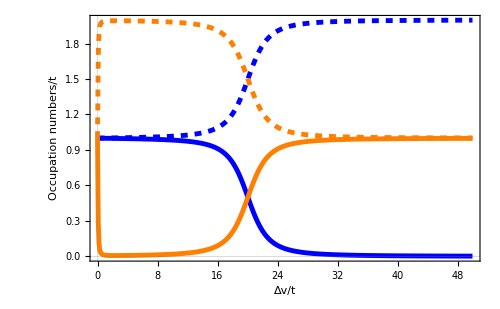

```mathematica
im41=With[{t=1.0,U=20.0},ListPlot[
{Table[Flatten[{Δv/t,Densite[t,U,Δv][[1]]}],{Δv,0.0,50,0.1}],
Table[Flatten[{Δv/t,Densite[t,U,Δv][[2]]}],{Δv,0.0,50,0.1}],
Table[Flatten[{Δv/t,Densite[t,U,Δv][[3]]}],{Δv,0.0,50,0.1}],
Table[Flatten[{Δv/t,Densite[t,U,Δv][[4]]}],{Δv,0.0,50,0.1}]},
Joined->True,Frame->True,FrameLabel->{"Δv/t","Occupation numbers/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotRange->All, PlotStyle->{{Blue,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Orange,Thickness[0.007]},{Dashed,Orange,Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]}}
]]  //Quiet
```

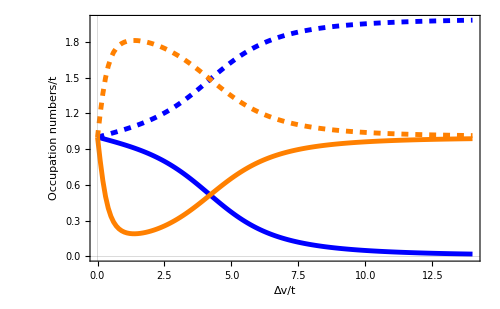

```mathematica
im42=With[{t=1.0,U=4.0},ListPlot[
{Table[Flatten[{Δv/t,Densite[t,U,Δv][[1]]}],{Δv,0.0,14,0.1}],
Table[Flatten[{Δv/t,Densite[t,U,Δv][[2]]}],{Δv,0.0,14,0.1}],
Table[Flatten[{Δv/t,Densite[t,U,Δv][[3]]}],{Δv,0.0,14,0.1}],
Table[Flatten[{Δv/t,Densite[t,U,Δv][[4]]}],{Δv,0.0,14,0.1}]},
Joined->True,Frame->True,FrameLabel->{"Δv/t","Occupation numbers/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotRange->All, PlotStyle->{{Blue,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Orange,Thickness[0.007]},{Dashed,Orange,Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]}}
]]  //Quiet
```

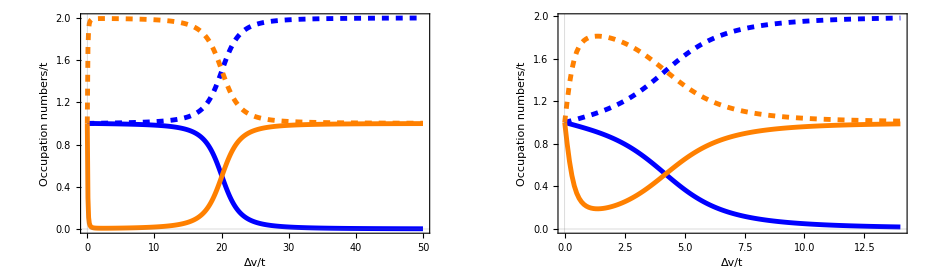

```mathematica
n=Legended[GraphicsGrid[{{im41,im42}},ImageSize->925],LineLegend[{Blue,{Dashed,Blue},Orange,{Dashed,Orange},White},{"<(n̂)_1>_0","<(n̂)_2>_0","<(n̂)_1>_1","<(n̂)_2>_1","                            "},LabelStyle->Directive[FontFamily->"Arial",20]]]
```

```mathematica
figs=GraphicsColumn[{Excneutres,Eb,d,n}]
```

-Graphics-

```mathematica
Series[-2t+√(16 t^2+U^2),{U,0,4},Assumptions->t>0]//FullSimplify
Series[√(4 t^2+4U t),{U,0,4},Assumptions->t>0]//FullSimplify
```

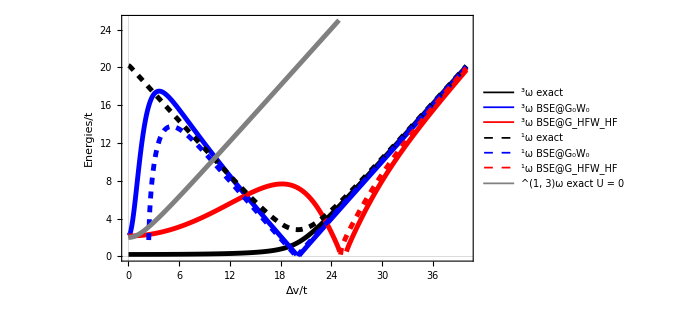

```mathematica
BSEWωGzGhfDv=With[{t=N[1,150],U=N[20,150]},ListPlot[
{Table[Flatten[{Δv,excas1[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[1,2]]}],{Δv,0,40,0.1}],
BSEWGhfωtriplet,
Table[Flatten[{Δv,excas2[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[2,2]]}],{Δv,0,40,0.1}],
BSEWGhfωsingulet,
Table[Flatten[{Δv,excas1[t,0,Δv]}],{Δv,0,40,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@G_0W_0","^3ω BSE@G_HFW_HF","^1ω exact","^1ω BSE@G_0W_0","^1ω BSE@G_HFW_HF","^(1, 3)ω exact U = 0"},Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotRange->{{0,40},{0,25}},PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Gray,Thickness[0.007]}}]]//Quiet
```

```mathematica
Export["BSEWwGzGhfDv.pdf",BSEWωGzGhfDv]
```

BSEWwGzGhfDv.pdf

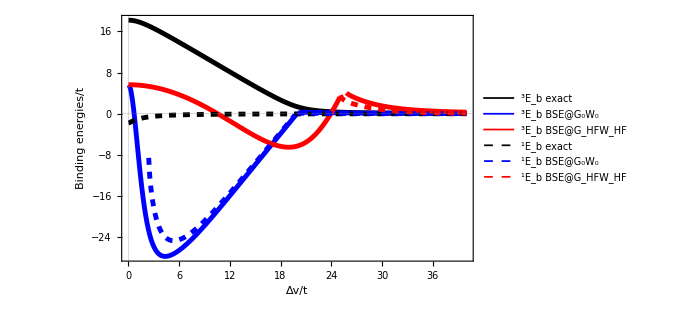

```mathematica
BSEWEbGzGhfDv=With[{t=N[1,150],U=N[20,150]},ListPlot[
{Table[Flatten[{Δv,Eb1exc[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[1,3]]}],{Δv,0,40,0.1}],
BSEWGhfEbtriplet,
Table[Flatten[{Δv,Eb2exc[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[2,3]]}],{Δv,0,40,0.1}],
BSEWGhfEbsingulet},
Joined->True,PlotLegends->{"^3E_b exact","^3E_b BSE@G_0W_0","^3E_b BSE@G_HFW_HF","^1E_b exact","^1E_b BSE@G_0W_0","^1E_b BSE@G_HFW_HF"},Frame->True,FrameLabel->{"Δv/t","Binding energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotRange->All,PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Red,Thickness[0.007]}}]]//Quiet
```

```mathematica
Export["BSEWEbGzGhfDv.pdf",BSEWEbGzGhfDv]
```

BSEWEbGzGhfDv.pdf

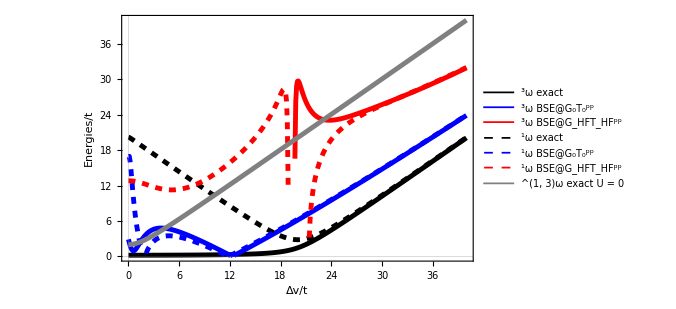

```mathematica
BSETppwGzGhfDv=With[{t=N[1.0,150],U=N[20,150]},ListPlot[
{Table[Flatten[{Δv,excas1[t,U,Δv]}],{Δv,0,40,0.1}],
BSETppGzωtriplet,
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[1,2]]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,excas2[t,U,Δv]}],{Δv,0,40,0.1}],
BSETppGzωsingulet,
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[2,2]]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,excas1[t,0,Δv]}],{Δv,0,40,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@G_0T_0^pp","^3ω BSE@G_HFT_HF^pp","^1ω exact","^1ω BSE@G_0T_0^pp","^1ω BSE@G_HFT_HF^pp","^(1, 3)ω exact U = 0"},Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Gray,Thickness[0.007]}}]] //Quiet
```

```mathematica
Export["BSEwTppGzGhfDv.pdf",BSETppwGzGhfDv]
```

BSEwTppGzGhfDv.pdf

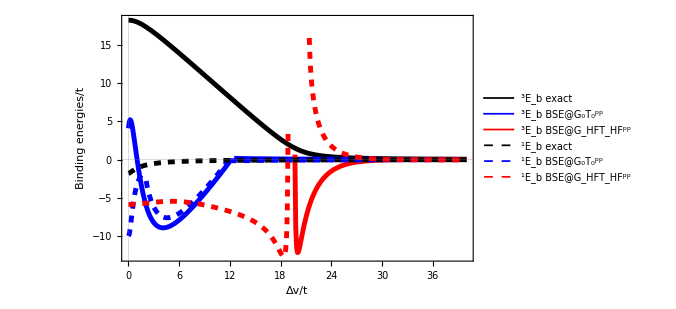

```mathematica
BSETppEbGzGhfDv=With[{t=N[1,150],U=N[20,150]},ListPlot[
{Table[Flatten[{Δv,Eb1exc[t,U,Δv]}],{Δv,0,40,0.1}],
BSETppGzEbtriplet,
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[1,3]]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,Eb2exc[t,U,Δv]}],{Δv,0,40,0.1}],
BSETppGzEbsingulet,
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[2,3]]}],{Δv,0,40,0.1}]},
Joined->True,PlotLegends->{"^3E_b exact","^3E_b BSE@G_0T_0^pp","^3E_b BSE@G_HFT_HF^pp","^1E_b exact","^1E_b BSE@G_0T_0^pp","^1E_b BSE@G_HFT_HF^pp"},Frame->True,FrameLabel->{"Δv/t","Binding energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotRange->All,PlotStyle->{{Black,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Red,Thickness[0.007]}}]]//Quiet
```

```mathematica
Export["BSETppEbGzGhfDv.pdf",BSETppEbGzGhfDv]
```

BSETppEbGzGhfDv.pdf

```mathematica
Export["Transitions_GzW.pdf",transtionGzW]
```

Transitions_GzW.pdf

```mathematica
BSE[1.0,20.0,5.0]
```

{{-10.9131,16.641,-27.5541,0.525226,-0.999163},{-10.9131,13.7402,-24.6533,-2.93769-3.59763×10^-16 ⅈ,-0.988764}}

```mathematica
Export["Transitions_GzTpp_U.pdf",transtionGT0ppU]
```

Transitions_GzTpp_U.pdf

```mathematica
c10[t_,Δv_]:=1/(√(1+(Δv/(2t)+√((Δv/(2t))^2+1))^2));c20[t_,Δv_]:=(Δv/(2t)+√((Δv/(2t))^2+1))/(√(1+(Δv/(2t)+√((Δv/(2t))^2+1))^2)); 
c11[t_,Δv_]:=1/(√(1+(Δv/(2t)-√((Δv/(2t))^2+1))^2));c21[t_,Δv_]:=(Δv/(2t)-√((Δv/(2t))^2+1))/(√(1+(Δv/(2t)-√((Δv/(2t))^2+1))^2));
d[t_,Δv_]:=√(4 t^2+Δv^2); dt[t_,U_,Δv_]:=√(d[t,Δv]^2-(4U t^2)/d[t,Δv]);
A[t_,Δv_]:=1/2-Δv/(2d[t,Δv]);B[t_,Δv_]:=1/2+Δv/(2d[t,Δv]);
Σ11[ω_,t_,U_,Δv_]:=A[t,Δv]U+(U^2 t^2)/(d[t,Δv]dt[t,U,Δv])(B[t,Δv]/(ω-(d[t,Δv]/2+dt[t,U,Δv]))+A[t,Δv]/(ω+(d[t,Δv]/2+dt[t,U,Δv])));
Σ22[ω_,t_,U_,Δv_]:=B[t,Δv]U+(U^2 t^2)/(d[t,Δv]dt[t,U,Δv])(A[t,Δv]/(ω-(d[t,Δv]/2+dt[t,U,Δv]))+B[t,Δv]/(ω+(d[t,Δv]/2+dt[t,U,Δv])));
```

```mathematica
Σ12[ω_,t_,U_,Δv_]:=(U^2 t^3)/(d[t,Δv]^2 dt[t,U,Δv])(1/(ω-(d[t,Δv]/2+dt[t,U,Δv]))-1/(ω+(d[t,Δv]/2+dt[t,U,Δv])));
Σvv[ω_,t_,U_,Δv_]:=c10[t,Δv]^2 Σ11[ω,t,U,Δv]+2c10[t,Δv]c20[t,Δv]Σ12[ω,t,U,Δv]+c20[t,Δv]^2 Σ22[ω,t,U,Δv]
dΣ11[ω_,t_,U_,Δv_]:=-(U^2 t^2)/(d[t,Δv]dt[t,U,Δv])(B[t,Δv]/(ω-(d[t,Δv]/2+dt[t,U,Δv]))^2+A[t,Δv]/(ω+(d[t,Δv]/2+dt[t,U,Δv]))^2);
dΣ22[ω_,t_,U_,Δv_]:=-(U^2 t^2)/(d[t,Δv]dt[t,U,Δv])(A[t,Δv]/(ω-(d[t,Δv]/2+dt[t,U,Δv]))^2+B[t,Δv]/(ω+(d[t,Δv]/2+dt[t,U,Δv]))^2);
dΣ12[ω_,t_,U_,Δv_]:=-(U^2 t^3)/(d[t,Δv]^2 dt[t,U,Δv])(1/(ω-(d[t,Δv]/2+dt[t,U,Δv]))^2-1/(ω+(d[t,Δv]/2+dt[t,U,Δv]))^2);
dΣvv[ω_,t_,U_,Δv_]:=c10[t,Δv]^2 dΣ11[ω,t,U,Δv]+2c10[t,Δv]c20[t,Δv]dΣ12[ω,t,U,Δv]+c20[t,Δv]^2 dΣ22[ω,t,U,Δv];
dΣcc[ω_,t_,U_,Δv_]:=c11[t,Δv]^2 dΣ11[ω,t,U,Δv]+2c11[t,Δv]c21[t,Δv]dΣ12[ω,t,U,Δv]+c21[t,Δv]^2 dΣ22[ω,t,U,Δv];

Zvv[ω_,t_,U_,Δv_]:=(1-dΣvv[ω,t,U,Δv])^-1;
Zcc[ω_,t_,U_,Δv_]:=(1-dΣcc[ω,t,U,Δv])^-1;
```

```mathematica
c[t_,U_]:=√(16 t^2+U^2)
a[t_,U_]:=√(2((16 t^2)/(c[t,U]-U)^2+1))
```

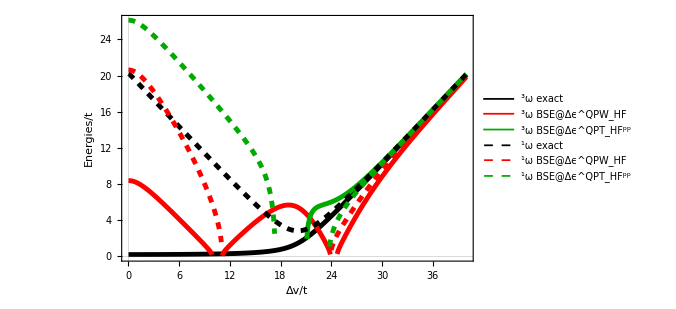

```mathematica
ωQPexact=With[{t=N[1,150],U=N[20,150]},ListPlot[
{Table[Flatten[{Δv,excas1[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[1,2]]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[1,2]]}],{Δv,0,40,0.1}], 
Table[Flatten[{Δv,excas2[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[2,2]]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[2,2]]}],{Δv,0,40,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@Δϵ^QPW_HF","^3ω BSE@Δϵ^QPT_HF^pp","^1ω exact","^1ω BSE@Δϵ^QPW_HF","^1ω BSE@Δϵ^QPT_HF^pp"},Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotRange->All,PlotStyle->{{Black,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]}}]]//Quiet
```

```mathematica
Export["Transitions_BSEW_BSEGT_eQP.pdf",ωQPexact]
```

Transitions_BSEW_BSEGT_eQP.pdf

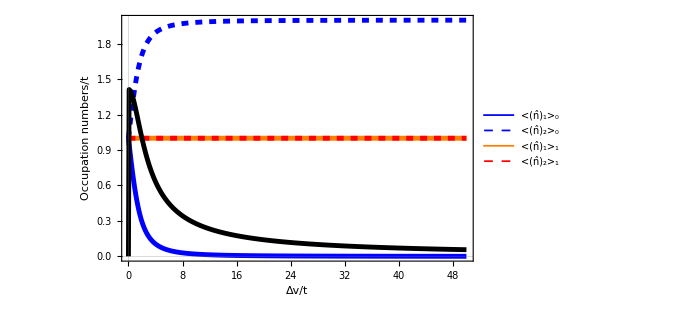

```mathematica
im41=With[{t=1.0,U=0.0},ListPlot[
{Table[Flatten[{Δv/t,Densite[t,U,Δv][[1]]}],{Δv,0.0,50,0.1}],
Table[Flatten[{Δv/t,Densite[t,U,Δv][[2]]}],{Δv,0.0,50,0.1}],
Table[Flatten[{Δv/t,Densite[t,U,Δv][[3]]}],{Δv,0.0,50,0.1}],
Table[Flatten[{Δv/t,Densite[t,U,Δv][[4]]}],{Δv,0.0,50,0.1}],
Table[Flatten[{Δv/t,Densite[t,U,Δv][[5]]-Densite[t,U,Δv][[6]]}],{Δv,0.0,50,0.1}]},
Joined->True,PlotLegends->{"<(n̂)_1>_0","<(n̂)_2>_0","<(n̂)_1>_1","<(n̂)_2>_1"}, Frame->True,FrameLabel->{"Δv/t","Occupation numbers/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotRange->All, PlotStyle->{{Blue,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Orange,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Black,Thickness[0.007]}}
]]  //Quiet
```

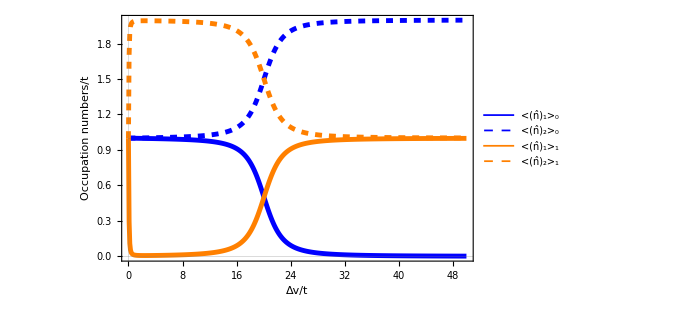

```mathematica
im41=With[{t=1.0,U=20.0},ListPlot[
{Table[Flatten[{Δv,Densite[t,U,Δv][[1]]}],{Δv,0.0,50,0.1}],
Table[Flatten[{Δv,Densite[t,U,Δv][[2]]}],{Δv,0.0,50,0.1}],
Table[Flatten[{Δv,Densite[t,U,Δv][[3]]}],{Δv,0.0,50,0.1}],
Table[Flatten[{Δv,Densite[t,U,Δv][[4]]}],{Δv,0.0,50,0.1}]},
Joined->True,PlotLegends->{"<(n̂)_1>_0","<(n̂)_2>_0","<(n̂)_1>_1","<(n̂)_2>_1"}, Frame->True,FrameLabel->{"Δv/t","Occupation numbers/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotRange->All, PlotStyle->{{Blue,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Orange,Thickness[0.007]},{Dashed,Orange,Thickness[0.007]}}
]]  //Quiet
```

```mathematica
Gold=RGBColor[1.0,0.843,0.0];
```

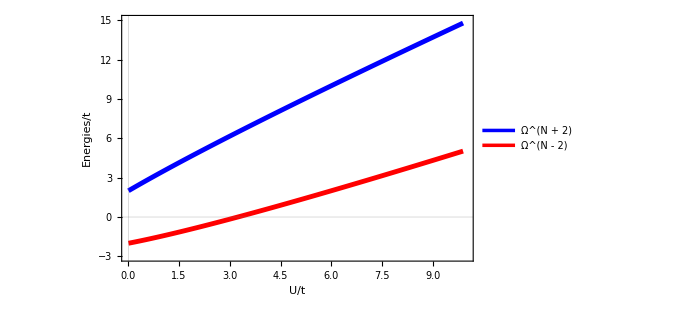

```mathematica
With[{t=N[1.0,150],Δv=0.0},ListPlot[
{Table[Flatten[{U,HubbardGT[t,U,Δv][[1]]}],{U,0.0001,10,0.1}],
Table[Flatten[{U,HubbardGT[t,U,Δv][[2]]}],{U,0.0001,10,0.1}]},
Joined->True,PlotLegends->{"Ω^(N + 2)","Ω^(N - 2)"},PlotRange->{{0,10},{-3,15}},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Blue,Thickness[0.007]},{Red,Thickness[0.007]}}]] //Quiet
```

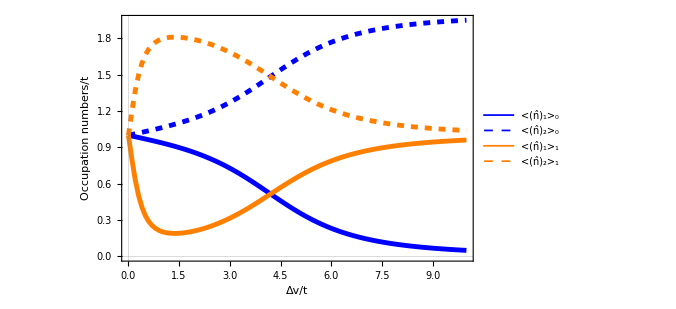

```mathematica
With[{t=1.0,U=4.0},ListPlot[
{Table[Flatten[{Δv,Densite[t,U,Δv][[1]]}],{Δv,0.0,10,0.1}],
Table[Flatten[{Δv,Densite[t,U,Δv][[2]]}],{Δv,0.0,10,0.1}],
Table[Flatten[{Δv,Densite[t,U,Δv][[3]]}],{Δv,0.0,10,0.1}],
Table[Flatten[{Δv,Densite[t,U,Δv][[4]]}],{Δv,0.0,10,0.1}]},
Joined->True,PlotLegends->{"<(n̂)_1>_0","<(n̂)_2>_0","<(n̂)_1>_1","<(n̂)_2>_1"}, Frame->True,FrameLabel->{"Δv/t","Occupation numbers/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotRange->All, PlotStyle->{{Blue,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Orange,Thickness[0.007]},{Dashed,Orange,Thickness[0.007]}}
]]  //Quiet
```

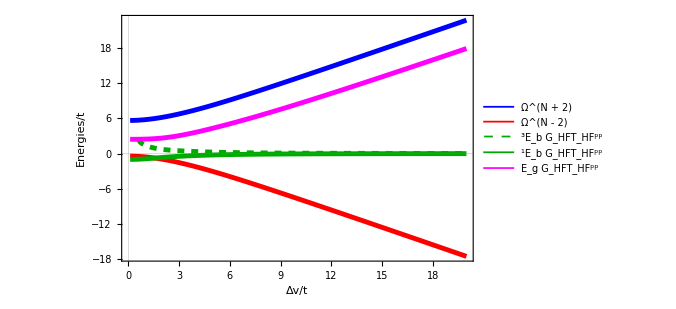

```mathematica
With[{t=N[1.0,150],U=2.6},ListPlot[
{Table[Flatten[{Δv,HubbardGT[t,U,Δv][[1]]}],{Δv,0.1,20,0.1}],
Table[Flatten[{Δv,HubbardGT[t,U,Δv][[2]]}],{Δv,0.1,20,0.1}],
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[1,3]]}],{Δv,0.1,20,0.1}],
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[2,3]]}],{Δv,0.1,20,0.1}],
Table[Flatten[{Δv,HubbardGT[t,U,Δv][[8]]}],{Δv,0.1,20,0.1}]},
Joined->True,PlotLegends->{"Ω^(N + 2)","Ω^(N - 2)","^3E_b G_HFT_HF^pp","^1E_b G_HFT_HF^pp","E_g G_HFT_HF^pp"},PlotRange->Automatic,Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]}}]] //Quiet
```

```mathematica
Export["BSETph_Eb_triplet_plusieurs_Dv.pdf",BSETphEbtriplet];
```

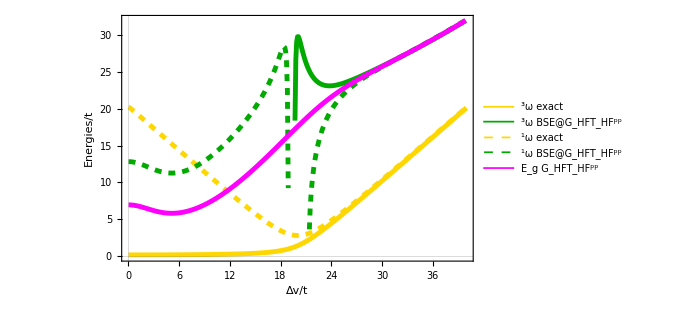

```mathematica
With[{t=1.0,U=20.0},ListPlot[
{Table[Flatten[{Δv,excas1[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[1,2]]}],{Δv,0.01,40,0.1}],
Table[Flatten[{Δv,excas2[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[2,2]]}],{Δv,0.01,40,0.1}],
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[1,1]]}],{Δv,0.01,40,0.1}]},
Joined->True,Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],PlotLegends->{"^3ω exact","^3ω BSE@G_HFT_HF^pp","^1ω exact","^1ω BSE@G_HFT_HF^pp","E_g G_HFT_HF^pp"},ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Gold,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Gold,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]}}
]]  //Quiet
```

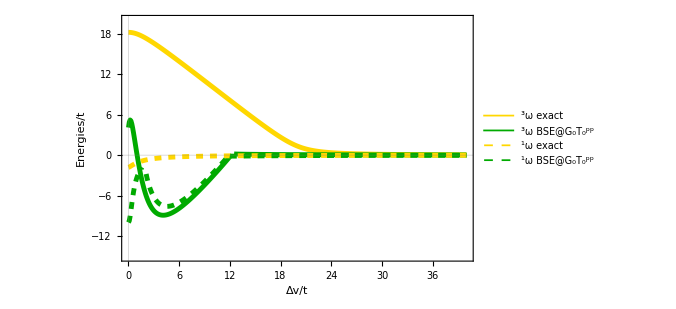

```mathematica
BSETppEBGzGhfDv=With[{t=N[1.0,150],U=N[20,150]},ListPlot[
{Table[Flatten[{Δv,Eb1exc[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSETppG0[t,U,Δv][[1,3]]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,Eb2exc[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSETppG0[t,U,Δv][[2,3]]}],{Δv,0,40,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@G_0T_0^pp","^1ω exact","^1ω BSE@G_0T_0^pp"},PlotRange->{{0,40},{-15,20}},Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Gold,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Gold,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]}}]] //Quiet
```

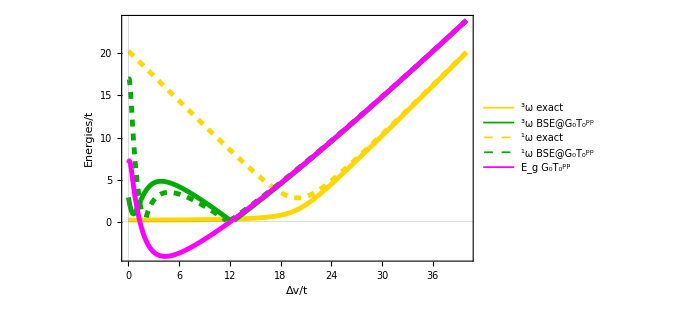

```mathematica
BSETppwGzGhfDv=With[{t=N[1.0,150],U=N[20,150]},ListPlot[
{Table[Flatten[{Δv,excas1[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSETppG0[t,U,Δv][[1,2]]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,excas2[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSETppG0[t,U,Δv][[2,2]]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSETppG0[t,U,Δv][[1,1]]}],{Δv,0,40,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@G_0T_0^pp","^1ω exact","^1ω BSE@G_0T_0^pp","E_g G_0T_0^pp"},Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Gold,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Gold,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]}}]] //Quiet
```

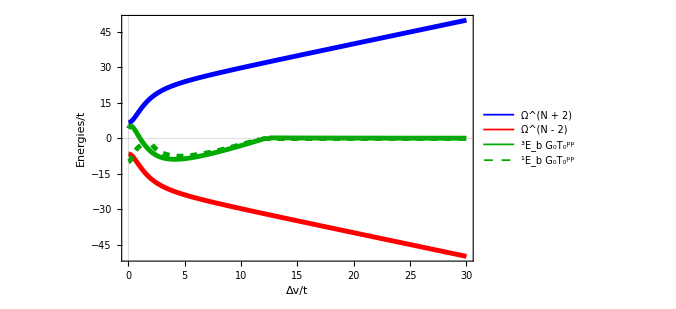

```mathematica
polesTpp=With[{t=N[1.0,150],U=20.0},ListPlot[
{Table[Flatten[{Δv,BSETppG0[t,U,Δv][[1,6]]}],{Δv,0,30,0.1}],
Table[Flatten[{Δv,BSETppG0[t,U,Δv][[1,5]]}],{Δv,0,30,0.1}],
Table[Flatten[{Δv,BSETppG0[t,U,Δv][[1,3]]}],{Δv,0,30,0.1}],
Table[Flatten[{Δv,BSETppG0[t,U,Δv][[2,3]]}],{Δv,0,30,0.1}]},
Joined->True,PlotLegends->{"Ω^(N + 2)","Ω^(N - 2)","^3E_b G_0T_0^pp","^1E_b G_0T_0^pp"},Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]}}]] //Quiet
```

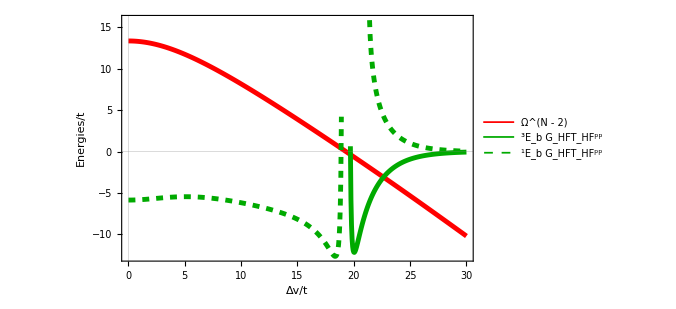

```mathematica
polesTpp=With[{t=N[1.0,150],U=20.0},ListPlot[
{Table[Flatten[{Δv,HubbardGT[t,U,Δv][[2]]}],{Δv,0,30,0.1}],
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[1,3]]}],{Δv,0,30,0.05}],
Table[Flatten[{Δv,BSEGTαβ[t,U,Δv][[2,3]]}],{Δv,0,30,0.05}]},
Joined->True,PlotLegends->{"Ω^(N - 2)","^3E_b G_HFT_HF^pp","^1E_b G_HFT_HF^pp"},Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]}}]] //Quiet
```

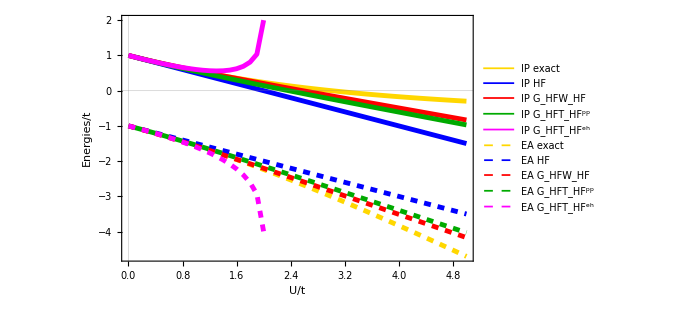

```mathematica
QPU=With[{t=1,Δv=0.0},ListPlot[
{Table[{U,ωEIexcas[t,U,Δv]},{U,0,5,0.1}],
Table[{U,-HubbardHF[t,U,Δv]⟦2,1⟧},{U,0,5,0.1}],
Table[{U,-HubbardGW[t,U,Δv]⟦3,1⟧},{U,0,5,0.1}],
Table[{U,-HubbardGT[t,U,Δv]⟦3,1⟧},{U,0,5,0.1}],
Table[{U,-HubbardGTehSpinOrb[t,U,Δv]⟦1,6,1⟧},{U,0,2.07,0.1}],
Table[{U,ωEAexcas[t,U,Δv]},{U,0,5,0.1}],
Table[{U,-HubbardHF[t,U,Δv]⟦2,2⟧},{U,0,5,0.1}],
Table[{U,-HubbardGW[t,U,Δv]⟦3,2⟧},{U,0,5,0.1}],
Table[{U,-HubbardGT[t,U,Δv]⟦3,2⟧},{U,0,5,0.1}],
Table[{U,-HubbardGTehSpinOrb[t,U,Δv]⟦1,6,2⟧},{U,0,2.07,0.1}]},
Joined->True,PlotStyle->{{Gold,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]},{Dashed,Gold,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Magenta,Thickness[0.007]}},Frame->True,PlotLegends->{"IP exact","IP HF","IP G_HFW_HF","IP G_HFT_HF^pp","IP G_HFT_HF^eh","EA exact","EA HF","EA G_HFW_HF","EA G_HFT_HF^pp","EA G_HFT_HF^eh"},FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[White,FontSize->20],FrameStyle->Directive[White,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"
]] //Quiet
```

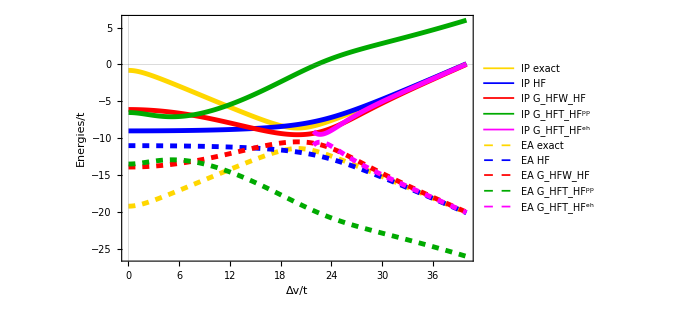

```mathematica
gr22=With[{t=1,U=20.0},ListPlot[
{Table[{Δv,ωEIexcas[t,U,Δv]},{Δv,0,40,0.1}],
Table[{Δv,-HubbardHF[t,U,Δv]⟦2,1⟧},{Δv,0,40,0.1}],
Table[{Δv,-HubbardGW[t,U,Δv]⟦3,1⟧},{Δv,0,40,0.1}],
Table[{Δv,-HubbardGT[t,U,Δv]⟦3,1⟧},{Δv,0,40,0.1}],
Table[{Δv,-HubbardGTehSpinOrb[t,U,Δv]⟦1,6,1⟧},{Δv,21.9,40,0.1}],
Table[{Δv,ωEAexcas[t,U,Δv]},{Δv,0,40,0.1}],
Table[{Δv,-HubbardHF[t,U,Δv]⟦2,2⟧},{Δv,0,40,0.1}],
Table[{Δv,-HubbardGW[t,U,Δv]⟦3,2⟧},{Δv,0,40,0.1}],
Table[{Δv,-HubbardGT[t,U,Δv]⟦3,2⟧},{Δv,0,40,0.1}],
Table[{Δv,-HubbardGTehSpinOrb[t,U,Δv]⟦1,6,2⟧},{Δv,21.9,40,0.1}]},
Joined->True,PlotStyle->{{Gold,Thickness[0.007]},{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]},{Dashed,Gold,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Dashed,Magenta,Thickness[0.007]}},Frame->True,FrameLabel->{"Δv/t","Energies/t"},PlotLegends->{"IP exact","IP HF","IP G_HFW_HF","IP G_HFT_HF^pp","IP G_HFT_HF^eh","EA exact","EA HF","EA G_HFW_HF","EA G_HFT_HF^pp","EA G_HFT_HF^eh"},LabelStyle->Directive[White,FontSize->20],FrameStyle->Directive[White,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"
]] //Quiet
```

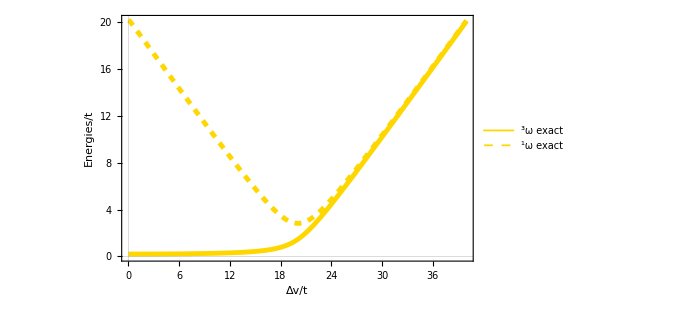

```mathematica
With[{t=N[1.0,150],U=N[20,150]},ListPlot[
{Table[Flatten[{Δv,excas1[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,excas2[t,U,Δv]}],{Δv,0,40,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^1ω exact"},Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Gold,Thickness[0.007]},{Dashed,Gold,Thickness[0.007]}}]] //Quiet
```

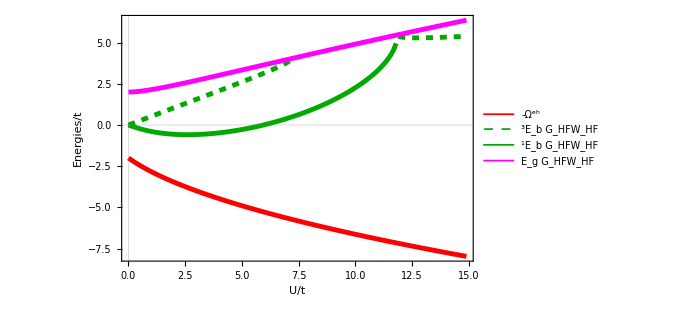

```mathematica
With[{t=N[1.0,150],Δv=0.0},ListPlot[
{Table[Flatten[{U,-HubbardGW[t,U,Δv][[1,1]]}],{U,0.0001,15,0.1}],
Table[Flatten[{U,BSE[t,U,Δv][[1,3]]}],{U,0.0001,15,0.1}],
Table[Flatten[{U,BSE[t,U,Δv][[2,3]]}],{U,0.0001,15,0.1}],
Table[Flatten[{U,HubbardGW[t,U,Δv][[8]]}],{U,0.0001,15,0.1}]},
Joined->True,PlotLegends->{"-Ω^eh","^3E_b G_HFW_HF","^1E_b G_HFW_HF","E_g G_HFW_HF"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Red,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]}}]] //Quiet
```

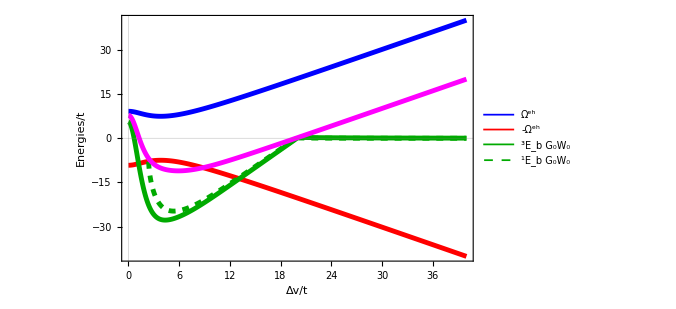

```mathematica
With[{t=N[1.0,150],U=N[20.0,150]},ListPlot[
{Table[Flatten[{Δv,HubbardGW[t,U,Δv][[1,1]]}],{Δv,0.0,40,0.1}],
Table[Flatten[{Δv,-HubbardGW[t,U,Δv][[1,1]]}],{Δv,0.0,40,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[1,3]]}],{Δv,0.0,40,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[2,3]]}],{Δv,0.0,40,0.01}],
Table[Flatten[{Δv,HubbardGW[t,U,Δv][[8]]}],{Δv,0.0,40,0.1}]},
Joined->True,PlotLegends->{"Ω^eh","-Ω^eh","^3E_b G_0W_0","^1E_b G_0W_0"},Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]}}]] //Quiet
```

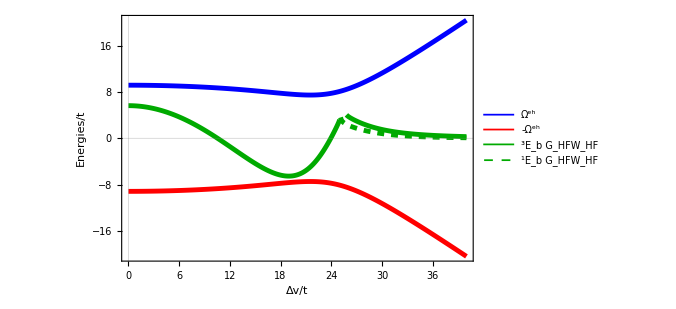

```mathematica
With[{t=N[1.0,150],U=N[20.0,150]},ListPlot[
{Table[Flatten[{Δv,HubbardGW[t,U,Δv][[1,1]]}],{Δv,0.0,40,0.1}],
Table[Flatten[{Δv,-HubbardGW[t,U,Δv][[1,1]]}],{Δv,0.0,40,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[1,3]]}],{Δv,0.0,40,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[2,3]]}],{Δv,0.0,40,0.1}]},
Joined->True,PlotLegends->{"Ω^eh","-Ω^eh","^3E_b G_HFW_HF","^1E_b G_HFW_HF"},Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]}}]] //Quiet
```

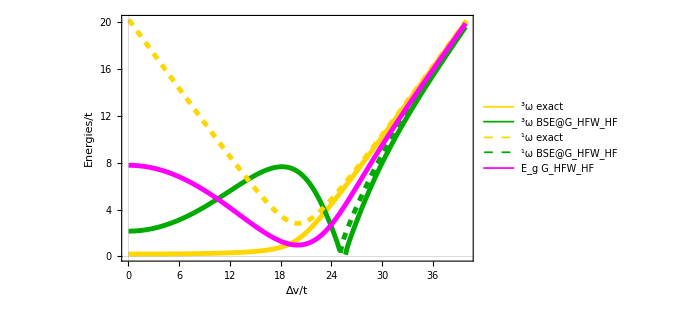

```mathematica
With[{t=1.0,U=20.0},ListPlot[
{Table[Flatten[{Δv,excas1[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[1,2]]}],{Δv,0.01,40,0.1}],
Table[Flatten[{Δv,excas2[t,U,Δv]}],{Δv,0,40,0.1}],
Table[Flatten[{Δv,BSE[t,U,Δv][[2,2]]}],{Δv,0.01,40,0.1}],
Table[Flatten[{Δv,HubbardGW[t,U,Δv][[8]]}],{Δv,0.01,40,0.1}]},
Joined->True,Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],PlotLegends->{"^3ω exact","^3ω BSE@G_HFW_HF","^1ω exact","^1ω BSE@G_HFW_HF","E_g G_HFW_HF"},ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Gold,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Gold,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]}}
]]  //Quiet
```

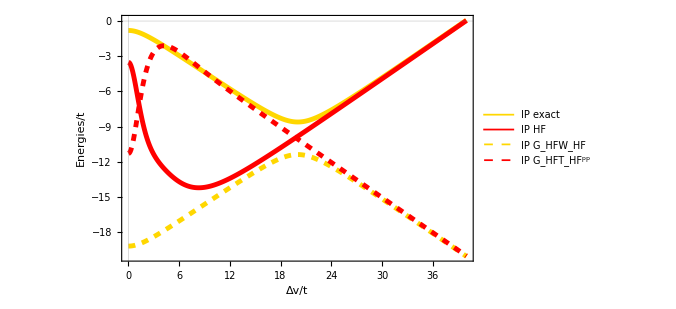

```mathematica
gr22=With[{t=1,U=20.0},ListPlot[
{Table[{Δv,ωEIexcas[t,U,Δv]},{Δv,0,40,0.1}],
Table[{Δv,-HubbardGW[t,U,Δv]⟦3,1⟧},{Δv,0,40,0.1}],
Table[{Δv,ωEAexcas[t,U,Δv]},{Δv,0,40,0.1}],
Table[{Δv,-HubbardGW[t,U,Δv]⟦3,2⟧},{Δv,0,40,0.1}]},
Joined->True,PlotStyle->{{Gold,Thickness[0.007]},{Red,Thickness[0.007]},{Dashed,Gold,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Gold,Thickness[0.007]},{Red,Thickness[0.007]}},Frame->True,FrameLabel->{"Δv/t","Energies/t"},PlotLegends->{"IP exact","IP HF","IP G_HFW_HF","IP G_HFT_HF^pp","IP G_HFT_HF^eh","EA exact","EA HF","EA G_HFW_HF","EA G_HFT_HF^pp","EA G_HFT_HF^eh"},LabelStyle->Directive[Black,FontSize->20],FrameStyle->Directive[Black,Thick],PlotRange->Automatic,ImageSize->500,PlotTheme->"Scientific"
]] //Quiet
```

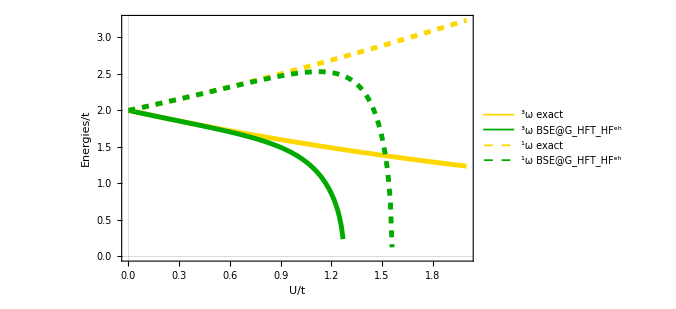

```mathematica
With[{t=1.0,Δv=0.0},ListPlot[
{Table[Flatten[{U,excas1[t,U,Δv]}],{U,0,2,0.1}],
Table[Flatten[{U,HubbardGTehSpinOrb[t,U,0.0][[1,2]]}],{U,0,1.95,0.01}],
Table[Flatten[{U,excas2[t,U,Δv]}],{U,0,2,0.1}],
Table[Flatten[{U,HubbardGTehSpinOrb[t,U,0.0][[2,2]]}],{U,0,1.95,0.01}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@G_HFT_HF^eh","^1ω exact","^1ω BSE@G_HFT_HF^eh"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Gold,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Gold,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]}}
]] //Quiet
```

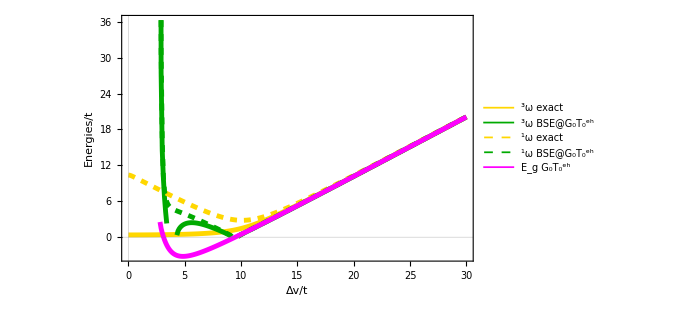

```mathematica
With[{t=1.0,U=10.0},ListPlot[
{Table[Flatten[{Δv,excas1[t,U,Δv]}],{Δv,0,30,0.1}],
Table[Flatten[{Δv,HubbardGTehSpinOrb[t,U,Δv][[1,2]]}],{Δv,1.8,30,0.1}],
Table[Flatten[{Δv,excas2[t,U,Δv]}],{Δv,0,30,0.1}],
Table[Flatten[{Δv,HubbardGTehSpinOrb[t,U,Δv][[2,2]]}],{Δv,1.8,30,0.1}],
Table[Flatten[{Δv,HubbardGTehSpinOrb[t,U,Δv][[1,1]]}],{Δv,1.8,30,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@G_0T_0^eh","^1ω exact","^1ω BSE@G_0T_0^eh","E_g G_0T_0^eh"},Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Gold,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Gold,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]}}
]] //Quiet
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

Max::nord: Invalid comparison with ComplexInfinity attempted.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigensystem::inf: Input matrix contains an infinite entry.

Set::shape: Lists {ω1$334907,V1$334907} and Transpose[Transpose[Eigensystem[{{ComplexInfinity,Indeterminate,Indeterminate,Indeterminate,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-3.+0. ⅈ},{0.+0. ⅈ,0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,7.5+0. ⅈ,0.+0. ⅈ},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.+0. ⅈ,-1.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{«1»},{«1»},{0.+0. ⅈ,0.+0. ⅈ,-7.5+0. ⅈ,«2»,-0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,1.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{3.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,Indeterminate,Indeterminate,Indeterminate,ComplexInfinity}}]]] are not the same shape.

Eigensystem::mindet: Input matrix contains an indeterminate entry.

Set::shape: Lists {λt$334907,Vt$334907} and Transpose[Transpose[Eigensystem[{{Indeterminate,3.+0. ⅈ},{-3.+0. ⅈ,Indeterminate}}]]] are not the same shape.

Eigensystem::mindet: Input matrix contains an indeterminate entry.

Set::shape: Lists {λs$334907,Vs$334907} and Transpose[Transpose[Eigensystem[{{Indeterminate,-3.+0. ⅈ},{3.+0. ⅈ,Indeterminate}}]]] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[λt$334907,Positive].

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

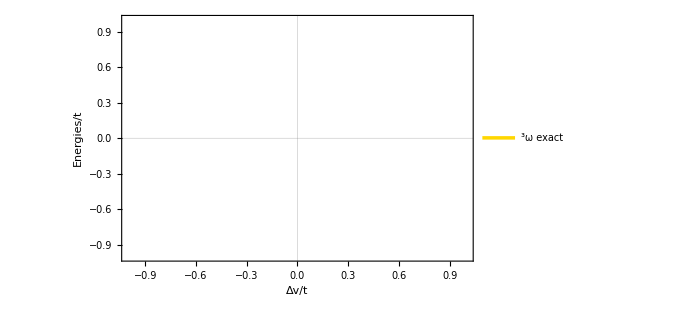

```mathematica
With[{t=N[1,200],U=N[3,200]},ListPlot[
{Table[Flatten[{Δv,HubbardGTehSpinOrb[t,U,0.0][[1,2]]}],{Δv,0,30,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@G_HFT_HF^eh","^1ω exact","^1ω BSE@G_HFT_HF^eh","E_g G_HFT_HF^eh"},Frame->True,FrameLabel->{"Δv/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Gold,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Gold,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]},{Magenta,Thickness[0.007]}}
]]
```

```mathematica
HubbardGTehSpinOrb[1.0,10,1][[1,1]]
```

Min::nord: Invalid comparison with 6.50598+4.2279×10^-16 ⅈ attempted.

Min::nord: Invalid comparison with 3.26607-1.97684 ⅈ attempted.

Max::nord: Invalid comparison with 3.49402+3.29363×10^-16 ⅈ attempted.

Max::nord: Invalid comparison with 2.16173×10^16+2.8823×10^16 ⅈ attempted.

Part::partw: Part 1 of {} does not exist.

-Max[3.49402+3.29363×10^-16 ⅈ,2.16173×10^16+2.8823×10^16 ⅈ]+Min[3.26607-1.97684 ⅈ,6.50598+4.2279×10^-16 ⅈ]